```mathematica
SetDirectory[NotebookDirectory[]];
<<"RadialPerturbationsEigenfunctions.wl"
```

## Applications 2x2

### Test 1

```mathematica
Block[{ΘMatrix,RMatrix,
transformedΘMatrix,SMatrix,TUMatrix,
x,y,PMatrix,approxSolutions},


Print["Exact solutions"];
{x[r_],y[r_]}={x[r],y[r]}//.DSolve[
{x'[r]==1/r x[r]+2/r y[r]+ r x[r],
y'[r]==-2/r x[r]-3/r y[r]+r  y[r]},
{x[r],y[r]},r,IncludeSingularSolutions->True
][[1]];

Print[
"x[r]= ", x[r],
"\ny[r]= ",y[r]
];
Print["Series expansion of exact solutions"];
Print[
"x[r]= ", Series[x[r],{r,0,1}],
"\ny[r]= ",Series[y[r],{r,0,1}]
];

Print["\nApproximate solutions"];
RMatrix={{1,2},{-2,-3}};
ΘMatrix={{r,0},{0, r}};


{SMatrix,transformedΘMatrix,TUMatrix}=EDOSystemReducer[RMatrix,ΘMatrix,r];
Print["SMatrix= ",SMatrix//MatrixForm];
Print["r^SMatrix= ",MatrixExp[Log[r]*SMatrix]//MatrixForm];

PMatrix=getPMatrixNoRec[SMatrix,transformedΘMatrix,2,r];
Print["PMatrix= ",PMatrix//MatrixForm];


approxSolutions=TUMatrix.PMatrix.MatrixExp[Log[r]*SMatrix].{{C[1]},{C[2]}};

Print[

{{"x[r]"},{"y[r]"}}//MatrixForm,"=",Collect[approxSolutions,{r}]//MatrixForm
];

(*Print[
"x[r]= ", Series[x[r],{r,0,1}]//Expand,
"\ny[r]= ",Series[y[r],{r,0,1}]//Expand
];*)


]
```

Exact solutions

x[r]= (ⅇ^(r^2/2) C[1])/r+(ⅇ^(r^2/2) C[2] Log[r])/r
y[r]= -(ⅇ^(r^2/2) C[1])/r+(ⅇ^(r^2/2) C[2] (1-2 Log[r]))/(2 r)

Series expansion of exact solutions

x[r]= (C[1]+C[2] Log[r])/r+1/2 (C[1]+C[2] Log[r]) r+O[r]^2
y[r]= (-2 C[1]+C[2]-2 C[2] Log[r])/(2 r)+1/4 (-2 C[1]+C[2]-2 C[2] Log[r]) r+O[r]^2

Approximate solutions

SMatrix= (1 | 2
-2 | -3)

r^SMatrix= ((1+2 Log[r])/r | (2 Log[r])/r
-(2 Log[r])/r | (1-2 Log[r])/r)

PMatrix= (1+r^2/2 | 0
0 | 1+r^2/2)

(x[r]
y[r])=(r (C[1]/2+C[1] Log[r]+C[2] Log[r])+(C[1]+2 C[1] Log[r]+2 C[2] Log[r])/r
(C[2]-2 C[1] Log[r]-2 C[2] Log[r])/r+r (C[2]/2-C[1] Log[r]-C[2] Log[r]))

### Test 2

```mathematica
Block[{ΘMatrix,RMatrix,
transformedΘMatrix,SMatrix,TUMatrix,
x,y,x2,y2,PMatrix,approxSolutions},

Print["Exact solutions"];
{x[r_],y[r_]}={x[r],y[r]}//.DSolve[
{x'[r]==-1/r x[r]+1/r y[r] +3 x[r]- y[r],
y'[r]==-2/r y[r]+3  y[r]},
{x[r],y[r]},r,IncludeSingularSolutions->True
][[1]];

Print[
"x[r]= ", x[r],
"\ny[r]= ",y[r]
];

Print[
"x[r]= ", Series[x[r],{r,0,1}],
"\ny[r]= ",Series[y[r],{r,0,1}]
];

Print["\nAproximate solutions"];
RMatrix={{-1,1},{0,-2}};
ΘMatrix={{3,-1},{0,3}};


{SMatrix,transformedΘMatrix,TUMatrix}=EDOSystemReducer[RMatrix,ΘMatrix,r];
Print["SMatrix= ",SMatrix//MatrixForm];
Print["TUMatrix= ",TUMatrix//MatrixForm];
Print["r^SMatrix= ",MatrixExp[Log[r]*SMatrix]//MatrixForm];

PMatrix=getPMatrixNoRec[SMatrix,transformedΘMatrix,3,r];
Print["PMatrix= ",PMatrix//MatrixForm];


approxSolutions=TUMatrix.PMatrix.MatrixExp[Log[r]*SMatrix].{{C[1]},{C[2]}};

Print[

{{"x[r]"},{"y[r]"}}//MatrixForm,"=",Collect[approxSolutions,{r}]//MatrixForm
];

(*Print[
"x[r]= ", Series[x[r],{r,0,1}]//Expand,
"\ny[r]= ",Series[y[r],{r,0,1}]//Expand
];*)


]
```

Exact solutions

x[r]= (ⅇ^(3 r) C[2])/r+(ⅇ^(3 r) C[1] (-1/r-Log[r]))/r
y[r]= (ⅇ^(3 r) C[1])/r^2

x[r]= -C[1]/r^2+(-3 C[1]+C[2]-C[1] Log[r])/r-3/2 (3 C[1]-2 C[2]+2 C[1] Log[r])-9/2 (C[1]-C[2]+C[1] Log[r]) r+O[r]^2
y[r]= C[1]/r^2+(3 C[1])/r+(9 C[1])/2+(9 C[1] r)/2+O[r]^2

Aproximate solutions

SMatrix= (-2 | 0
-1 | -2)

TUMatrix= (-1 | r
1 | 0)

r^SMatrix= (1/r^2 | 0
-Log[r]/r^2 | 1/r^2)

PMatrix= (1+3 r+(9 r^2)/2+(9 r^3)/2 | 0
0 | 1+3 r+(9 r^2)/2+(9 r^3)/2)

(x[r]
y[r])=(-(9 C[1])/2-C[1]/r^2+3 C[2]-3 C[1] Log[r]+r^2 ((9 C[2])/2-9/2 C[1] Log[r])+r (-(9 C[1])/2+(9 C[2])/2-9/2 C[1] Log[r])+(-3 C[1]+C[2]-C[1] Log[r])/r
(9 C[1])/2+C[1]/r^2+(3 C[1])/r+(9 r C[1])/2)

### Test 3

```mathematica
Block[{ΘMatrix,RMatrix,
transformedΘMatrix,SMatrix,TUMatrix,
x,y,z,PMatrix,approxSolutions},

Print["Exact solutions"];
{x[r_],y[r_]}={x[r],y[r]}//.DSolve[
{x'[r]==-1/r x[r]+3 r x[r]-r y[r],
y'[r]==-2/r y[r]-r^3 y[r]},
{x[r],y[r]},r,
IncludeSingularSolutions->True
][[1]];

Print[
"x[r]= ", x[r],
"\ny[r]= ",y[r]
];

Print[
"x[r]= ", Series[x[r],{r,0,10}],
"\ny[r]= ",Series[y[r],{r,0,10}]
];


Print["\nAproximate solutions"];
RMatrix={{-1,0},{0,-2}};
ΘMatrix={{3 r,-r},{0,-r^3}};


{SMatrix,transformedΘMatrix,TUMatrix}=EDOSystemReducer[RMatrix,ΘMatrix,r];

Print["r^SMatrix= ",MatrixExp[Log[r]*SMatrix]//MatrixForm];
Print["TUMatrix= ",TUMatrix//MatrixForm];
Print["transformedΘMatrix= ",transformedΘMatrix//MatrixForm];

PMatrix=getPMatrixNoRec[SMatrix,transformedΘMatrix,12,r];
Print["PMatrix= ",PMatrix//MatrixForm];

approxSolutions=Simplify[TUMatrix.PMatrix.MatrixExp[Log[r]*SMatrix].{{C[1]},{C[2]}}];


Print[
{{"x[r]"},{"y[r]"}}//MatrixForm, "=", Collect[approxSolutions,r]//MatrixForm
];


]
```

Exact solutions

x[r]= (ⅇ^((3 r^2)/2) C[2])/r+(ⅇ^((3 r^2)/2) C[1] -ⅇ^(-3/2 K[1]^2-K[1]^4/4)K[1]1r)/r
y[r]= (ⅇ^(-r^4/4) C[1])/r^2

x[r]= (C[2]-C[1] ∫_1^0 ⅇ^(-3/2 K[1]^2-K[1]^4/4)ⅆK[1])/r-C[1]+3/2 (C[2]-C[1] ∫_1^0 ⅇ^(-3/2 K[1]^2-K[1]^4/4)ⅆK[1]) r-C[1] r^2+((9 C[2])/8-9/8 C[1] ∫_1^0 ⅇ^(-3/2 K[1]^2-K[1]^4/4)ⅆK[1]) r^3-(11 C[1] r^4)/20+((9 C[2])/16-9/16 C[1] ∫_1^0 ⅇ^(-3/2 K[1]^2-K[1]^4/4)ⅆK[1]) r^5-(33 C[1] r^6)/140+((27 C[2])/128-27/128 C[1] ∫_1^0 ⅇ^(-3/2 K[1]^2-K[1]^4/4)ⅆK[1]) r^7-(827 C[1] r^8)/10080+((81 C[2])/1280-(81 C[1] ∫_1^0 ⅇ^(-3/2 K[1]^2-K[1]^4/4)ⅆK[1])/1280) r^9-(827 C[1] r^10)/36960+O[r]^11
y[r]= C[1]/r^2-(C[1] r^2)/4+(C[1] r^6)/32-(C[1] r^10)/384+O[r]^11

Aproximate solutions

r^SMatrix= (1/r^2 | 0
0 | 1/r^2)

TUMatrix= (0 | r
1 | 0)

transformedΘMatrix= (-r^3 | 0
-1 | 3 r)

PMatrix= (1-r^4/4+r^8/32-r^12/384 | 0
-r-r^3-(11 r^5)/20-(33 r^7)/140-(827 r^9)/10080-(827 r^11)/36960 | 1+(3 r^2)/2+(9 r^4)/8+(9 r^6)/16+(27 r^8)/128+(81 r^10)/1280+(81 r^12)/5120)

(x[r]
y[r])=(-C[1]-r^2 C[1]-(11 r^4 C[1])/20-(33 r^6 C[1])/140-(827 r^8 C[1])/10080-(827 r^10 C[1])/36960+C[2]/r+(3 r C[2])/2+(9 r^3 C[2])/8+(9 r^5 C[2])/16+(27 r^7 C[2])/128+(81 r^9 C[2])/1280+(81 r^11 C[2])/5120
C[1]/r^2-(r^2 C[1])/4+(r^6 C[1])/32-(r^10 C[1])/384)

### Dirac System

Exact solutions

x[r]= AiryAi[(r (1-λ)-(-1+λ) λ)/(1-λ)^(2/3)] C[1]+AiryBi[(r (1-λ)-(-1+λ) λ)/(1-λ)^(2/3)] C[2]
y[r]= (AiryAiPrime[(r (1-λ)-(-1+λ) λ)/(1-λ)^(2/3)] C[1])/(1-λ)^(2/3)+(AiryBiPrime[(r (1-λ)-(-1+λ) λ)/(1-λ)^(2/3)] C[2])/(1-λ)^(2/3)

x[r]= (AiryAi[-((-1+λ) λ)/(1-λ)^(2/3)] C[1]+AiryBi[-((-1+λ) λ)/(1-λ)^(2/3)] C[2])+((1-λ)^(1/3) AiryAiPrime[-((-1+λ) λ)/(1-λ)^(2/3)] C[1]+(1-λ)^(1/3) AiryBiPrime[-((-1+λ) λ)/(1-λ)^(2/3)] C[2]) r+O[r]^2
y[r]= (AiryAiPrime[-((-1+λ) λ)/(1-λ)^(2/3)] C[1]+AiryBiPrime[-((-1+λ) λ)/(1-λ)^(2/3)] C[2])/(1-λ)^(2/3)+(λ AiryAi[-((-1+λ) λ)/(1-λ)^(2/3)] C[1]+λ AiryBi[-((-1+λ) λ)/(1-λ)^(2/3)] C[2]) r+1/(2 (1-λ)^(2/3))((1-λ)^(2/3) AiryAi[-((-1+λ) λ)/(1-λ)^(2/3)] C[1]+λ AiryAiPrime[-((-1+λ) λ)/(1-λ)^(2/3)] C[1]-λ^2 AiryAiPrime[-((-1+λ) λ)/(1-λ)^(2/3)] C[1]+(1-λ)^(2/3) AiryBi[-((-1+λ) λ)/(1-λ)^(2/3)] C[2]+λ AiryBiPrime[-((-1+λ) λ)/(1-λ)^(2/3)] C[2]-λ^2 AiryBiPrime[-((-1+λ) λ)/(1-λ)^(2/3)] C[2]) r^2+O[r]^3

Aproximate solutions

r^SMatrix= (1 | 0
0 | 1)

TUMatrix= (1 | 0
0 | 1)

transformedΘMatrix= (0 | 1-λ
r+λ | 0)

PMatrix= (1+1/6 r^3 (1-λ)-1/2 r^2 (-1+λ) λ+1/30 r^5 (-1+λ)^2 λ+1/24 r^4 (-1+λ)^2 λ^2-1/560 r^7 (-1+λ)^3 λ^2-(r^10 (-1+λ)^4 λ^2 (-100-λ^3+λ^4))/3628800+(r^8 (-1+λ)^3 λ (-28-λ^3+λ^4))/40320+(r^13 (-1+λ)^5 λ^2 (-115-3 λ^3+3 λ^4))/518918400+(r^9 (-1+λ)^3 (-7-4 λ^3+4 λ^4))/90720-(r^11 (-1+λ)^4 λ (-56-5 λ^3+5 λ^4))/7983360-1/720 r^6 (-1+λ) (4-4 λ+λ^3-2 λ^4+λ^5)+(r^16 (-1+λ)^6 λ^2 (22960+1064 λ^3-1064 λ^4+λ^6-2 λ^7+λ^8))/20922789888000-(r^14 (-1+λ)^5 λ (3640+560 λ^3-560 λ^4+λ^6-2 λ^7+λ^8))/87178291200+(r^12 (-1+λ)^4 (280+260 λ^3-260 λ^4+λ^6-2 λ^7+λ^8))/479001600-(r^15 (-1+λ)^5 (520+680 λ^3-680 λ^4+7 λ^6-14 λ^7+7 λ^8))/186810624000+(r^17 (-1+λ)^6 λ (7280+1645 λ^3-1645 λ^4+8 λ^6-16 λ^7+8 λ^8))/44460928512000-(r^19 (-1+λ)^7 λ^2 (49840+3472 λ^3-3472 λ^4+9 λ^6-18 λ^7+9 λ^8))/13516122267648000-(r^22 (-1+λ)^8 λ^2 (-10077760-960960 λ^3+960960 λ^4-4620 λ^6+9240 λ^7-4620 λ^8-λ^9+3 λ^10-3 λ^11+λ^12))/1124000727777607680000+(r^20 (-1+λ)^7 λ (-1106560-336000 λ^3+336000 λ^4-3000 λ^6+6000 λ^7-3000 λ^8-λ^9+3 λ^10-3 λ^11+λ^12))/2432902008176640000-(r^18 (-1+λ)^6 (-58240-99120 λ^3+99120 λ^4-1848 λ^6+3696 λ^7-1848 λ^8-λ^9+3 λ^10-3 λ^11+λ^12))/6402373705728000+(r^25 (-1+λ)^9 λ^2 (-7114800-874720 λ^3+874720 λ^4-6545 λ^6+13090 λ^7-6545 λ^8-4 λ^9+12 λ^10-12 λ^11+4 λ^12))/430866945648082944000000+(r^21 (-1+λ)^7 (-55328-116592 λ^3+116592 λ^4-3318 λ^6+6636 λ^7-3318 λ^8-5 λ^9+15 λ^10-15 λ^11+5 λ^12))/2554547108585472000-(r^23 (-1+λ)^8 λ (-2213120-853440 λ^3+853440 λ^4-11760 λ^6+23520 λ^7-11760 λ^8-11 λ^9+33 λ^10-33 λ^11+11 λ^12))/2350183339898634240000+(r^24 (-1+λ)^8 (24344320+61378240 λ^3-61378240 λ^4+2420880 λ^6-4841760 λ^7+2420880 λ^8+6820 λ^9-20460 λ^10+20460 λ^11-6819 λ^12-4 λ^13+6 λ^14-4 λ^15+λ^16))/620448401733239439360000 | r (1-λ)+1/12 r^4 (-1+λ)^2+1/6 r^3 (-1+λ)^2 λ-1/120 r^6 (-1+λ)^3 λ-1/120 r^5 (-1+λ)^3 λ^2+(r^8 (-1+λ)^4 λ^2)/3360+(r^11 (-1+λ)^5 λ^2 (-160-λ^3+λ^4))/39916800-(r^14 (-1+λ)^6 λ^2 (-60-λ^3+λ^4))/2075673600-(r^9 (-1+λ)^4 λ (-52-λ^3+λ^4))/362880+(r^12 (-1+λ)^5 λ (-20-λ^3+λ^4))/15966720+(r^7 (-1+λ)^3 (-10-λ^3+λ^4))/5040-(r^10 (-1+λ)^4 (-4-λ^3+λ^4))/181440-(r^17 (-1+λ)^7 λ^2 (46480+1400 λ^3-1400 λ^4+λ^6-2 λ^7+λ^8))/355687428096000+(r^15 (-1+λ)^6 λ (8680+770 λ^3-770 λ^4+λ^6-2 λ^7+λ^8))/1307674368000+(r^20 (-1+λ)^8 λ^2 (10976+504 λ^3-504 λ^4+λ^6-2 λ^7+λ^8))/27032244535296000-(r^13 (-1+λ)^5 (880+380 λ^3-380 λ^4+λ^6-2 λ^7+λ^8))/6227020800-(r^18 (-1+λ)^7 λ (2100+280 λ^3-280 λ^4+λ^6-2 λ^7+λ^8))/88921857024000+(r^16 (-1+λ)^6 (220+140 λ^3-140 λ^4+λ^6-2 λ^7+λ^8))/373621248000+(r^23 (-1+λ)^9 λ^2 (-23826880-1515360 λ^3+1515360 λ^4-5610 λ^6+11220 λ^7-5610 λ^8-λ^9+3 λ^10-3 λ^11+λ^12))/25852016738884976640000-(r^21 (-1+λ)^8 λ (-3082240-562800 λ^3+562800 λ^4-3720 λ^6+7440 λ^7-3720 λ^8-λ^9+3 λ^10-3 λ^11+λ^12))/51090942171709440000+(r^19 (-1+λ)^7 (-209440-179760 λ^3+179760 λ^4-2352 λ^6+4704 λ^7-2352 λ^8-λ^9+3 λ^10-3 λ^11+λ^12))/121645100408832000+(r^24 (-1+λ)^9 λ (-545440-128520 λ^3+128520 λ^4-1320 λ^6+2640 λ^7-1320 λ^8-λ^9+3 λ^10-3 λ^11+λ^12))/4700366679797268480000-(r^22 (-1+λ)^8 (-38080-41664 λ^3+41664 λ^4-840 λ^6+1680 λ^7-840 λ^8-λ^9+3 λ^10-3 λ^11+λ^12))/10218188434341888000-(r^25 (-1+λ)^9 (96342400+129236800 λ^3-129236800 λ^4+3640560 λ^6-7281120 λ^7+3640560 λ^8+8140 λ^9-24420 λ^10+24420 λ^11-8139 λ^12-4 λ^13+6 λ^14-4 λ^15+λ^16))/15511210043330985984000000
r^2/2+r λ-1/6 r^4 (-1+λ) λ-1/6 r^3 (-1+λ) λ^2+1/80 r^6 (-1+λ)^2 λ^2+(r^9 (-1+λ)^3 λ^2 (-100-λ^3+λ^4))/362880-(r^7 (-1+λ)^2 λ (-28-λ^3+λ^4))/5040-(r^12 (-1+λ)^4 λ^2 (-115-3 λ^3+3 λ^4))/39916800-(r^8 (-1+λ)^2 (-7-4 λ^3+4 λ^4))/10080+(r^10 (-1+λ)^3 λ (-56-5 λ^3+5 λ^4))/725760+1/120 r^5 (4-4 λ+λ^3-2 λ^4+λ^5)-(r^15 (-1+λ)^5 λ^2 (22960+1064 λ^3-1064 λ^4+λ^6-2 λ^7+λ^8))/1307674368000+(r^13 (-1+λ)^4 λ (3640+560 λ^3-560 λ^4+λ^6-2 λ^7+λ^8))/6227020800-(r^11 (-1+λ)^3 (280+260 λ^3-260 λ^4+λ^6-2 λ^7+λ^8))/39916800+(r^14 (-1+λ)^4 (520+680 λ^3-680 λ^4+7 λ^6-14 λ^7+7 λ^8))/12454041600-(r^16 (-1+λ)^5 λ (7280+1645 λ^3-1645 λ^4+8 λ^6-16 λ^7+8 λ^8))/2615348736000+(r^18 (-1+λ)^6 λ^2 (49840+3472 λ^3-3472 λ^4+9 λ^6-18 λ^7+9 λ^8))/711374856192000+(r^21 (-1+λ)^7 λ^2 (-10077760-960960 λ^3+960960 λ^4-4620 λ^6+9240 λ^7-4620 λ^8-λ^9+3 λ^10-3 λ^11+λ^12))/51090942171709440000-(r^19 (-1+λ)^6 λ (-1106560-336000 λ^3+336000 λ^4-3000 λ^6+6000 λ^7-3000 λ^8-λ^9+3 λ^10-3 λ^11+λ^12))/121645100408832000+(r^17 (-1+λ)^5 (-58240-99120 λ^3+99120 λ^4-1848 λ^6+3696 λ^7-1848 λ^8-λ^9+3 λ^10-3 λ^11+λ^12))/355687428096000-(r^24 (-1+λ)^8 λ^2 (-7114800-874720 λ^3+874720 λ^4-6545 λ^6+13090 λ^7-6545 λ^8-4 λ^9+12 λ^10-12 λ^11+4 λ^12))/17234677825923317760000-(r^20 (-1+λ)^6 (-55328-116592 λ^3+116592 λ^4-3318 λ^6+6636 λ^7-3318 λ^8-5 λ^9+15 λ^10-15 λ^11+5 λ^12))/121645100408832000+(r^22 (-1+λ)^7 λ (-2213120-853440 λ^3+853440 λ^4-11760 λ^6+23520 λ^7-11760 λ^8-11 λ^9+33 λ^10-33 λ^11+11 λ^12))/102181884343418880000+(r^25 (-1+λ)^8 λ (608608000+286686400 λ^3-286686400 λ^4+5525520 λ^6-11051040 λ^7+5525520 λ^8+9724 λ^9-29172 λ^10+29172 λ^11-9723 λ^12-4 λ^13+6 λ^14-4 λ^15+λ^16))/15511210043330985984000000-(r^23 (-1+λ)^7 (24344320+61378240 λ^3-61378240 λ^4+2420880 λ^6-4841760 λ^7+2420880 λ^8+6820 λ^9-20460 λ^10+20460 λ^11-6819 λ^12-4 λ^13+6 λ^14-4 λ^15+λ^16))/25852016738884976640000 | 1+1/3 r^3 (1-λ)-1/2 r^2 (-1+λ) λ+1/20 r^5 (-1+λ)^2 λ+1/24 r^4 (-1+λ)^2 λ^2-1/420 r^7 (-1+λ)^3 λ^2-(r^10 (-1+λ)^4 λ^2 (-160-λ^3+λ^4))/3628800+(r^13 (-1+λ)^5 λ^2 (-60-λ^3+λ^4))/148262400+(r^8 (-1+λ)^3 λ (-52-λ^3+λ^4))/40320-(r^11 (-1+λ)^4 λ (-20-λ^3+λ^4))/1330560-1/720 r^6 (-1+λ)^2 (-10-λ^3+λ^4)+(r^9 (-1+λ)^3 (-4-λ^3+λ^4))/18144+(r^16 (-1+λ)^6 λ^2 (46480+1400 λ^3-1400 λ^4+λ^6-2 λ^7+λ^8))/20922789888000-(r^14 (-1+λ)^5 λ (8680+770 λ^3-770 λ^4+λ^6-2 λ^7+λ^8))/87178291200-(r^19 (-1+λ)^7 λ^2 (10976+504 λ^3-504 λ^4+λ^6-2 λ^7+λ^8))/1351612226764800+(r^12 (-1+λ)^4 (880+380 λ^3-380 λ^4+λ^6-2 λ^7+λ^8))/479001600+(r^17 (-1+λ)^6 λ (2100+280 λ^3-280 λ^4+λ^6-2 λ^7+λ^8))/4940103168000-(r^15 (-1+λ)^5 (220+140 λ^3-140 λ^4+λ^6-2 λ^7+λ^8))/23351328000-(r^22 (-1+λ)^8 λ^2 (-23826880-1515360 λ^3+1515360 λ^4-5610 λ^6+11220 λ^7-5610 λ^8-λ^9+3 λ^10-3 λ^11+λ^12))/1124000727777607680000+(r^20 (-1+λ)^7 λ (-3082240-562800 λ^3+562800 λ^4-3720 λ^6+7440 λ^7-3720 λ^8-λ^9+3 λ^10-3 λ^11+λ^12))/2432902008176640000-(r^18 (-1+λ)^6 (-209440-179760 λ^3+179760 λ^4-2352 λ^6+4704 λ^7-2352 λ^8-λ^9+3 λ^10-3 λ^11+λ^12))/6402373705728000+(r^25 (-1+λ)^9 λ^2 (-4127200-341880 λ^3+341880 λ^4-1980 λ^6+3960 λ^7-1980 λ^8-λ^9+3 λ^10-3 λ^11+λ^12))/99430833611096064000000-(r^23 (-1+λ)^8 λ (-545440-128520 λ^3+128520 λ^4-1320 λ^6+2640 λ^7-1320 λ^8-λ^9+3 λ^10-3 λ^11+λ^12))/195848611658219520000+(r^21 (-1+λ)^7 (-38080-41664 λ^3+41664 λ^4-840 λ^6+1680 λ^7-840 λ^8-λ^9+3 λ^10-3 λ^11+λ^12))/464463110651904000+(r^24 (-1+λ)^8 (96342400+129236800 λ^3-129236800 λ^4+3640560 λ^6-7281120 λ^7+3640560 λ^8+8140 λ^9-24420 λ^10+24420 λ^11-8139 λ^12-4 λ^13+6 λ^14-4 λ^15+λ^16))/620448401733239439360000)

(x[r]
y[r])=(C[1]+1/2 r^2 (1-λ) λ C[1]+r^4 (1/24 (-1+λ)^2 λ^2 C[1]+1/12 (-1+λ)^2 C[2])+r (C[2]-λ C[2])+r^3 (1/6 (1-λ) C[1]+1/6 (-1+λ)^2 λ C[2])+r^6 (1/720 (1-λ) (4-4 λ+λ^3-2 λ^4+λ^5) C[1]-1/120 (-1+λ)^3 λ C[2])+r^5 (1/30 (-1+λ)^2 λ C[1]-1/120 (-1+λ)^3 λ^2 C[2])+r^8 (((-1+λ)^3 λ (-28-λ^3+λ^4) C[1])/40320+((-1+λ)^4 λ^2 C[2])/3360)+r^11 (-((-1+λ)^4 λ (-56-5 λ^3+5 λ^4) C[1])/7983360+((-1+λ)^5 λ^2 (-160-λ^3+λ^4) C[2])/39916800)+r^14 (-((-1+λ)^5 λ (3640+560 λ^3-560 λ^4+λ^6-2 λ^7+λ^8) C[1])/87178291200-((-1+λ)^6 λ^2 (-60-λ^3+λ^4) C[2])/2075673600)+r^9 (((-1+λ)^3 (-7-4 λ^3+4 λ^4) C[1])/90720-((-1+λ)^4 λ (-52-λ^3+λ^4) C[2])/362880)+r^12 (((-1+λ)^4 (280+260 λ^3-260 λ^4+λ^6-2 λ^7+λ^8) C[1])/479001600+((-1+λ)^5 λ (-20-λ^3+λ^4) C[2])/15966720)+r^7 (-1/560 (-1+λ)^3 λ^2 C[1]+((-1+λ)^3 (-10-λ^3+λ^4) C[2])/5040)+r^10 (-((-1+λ)^4 λ^2 (-100-λ^3+λ^4) C[1])/3628800-((-1+λ)^4 (-4-λ^3+λ^4) C[2])/181440)+r^17 (((-1+λ)^6 λ (7280+1645 λ^3-1645 λ^4+8 λ^6-16 λ^7+8 λ^8) C[1])/44460928512000-((-1+λ)^7 λ^2 (46480+1400 λ^3-1400 λ^4+λ^6-2 λ^7+λ^8) C[2])/355687428096000)+r^15 (-((-1+λ)^5 (520+680 λ^3-680 λ^4+7 λ^6-14 λ^7+7 λ^8) C[1])/186810624000+((-1+λ)^6 λ (8680+770 λ^3-770 λ^4+λ^6-2 λ^7+λ^8) C[2])/1307674368000)+r^20 (((-1+λ)^7 λ (-1106560-336000 λ^3+336000 λ^4-3000 λ^6+6000 λ^7-3000 λ^8-λ^9+3 λ^10-3 λ^11+λ^12) C[1])/2432902008176640000+((-1+λ)^8 λ^2 (10976+504 λ^3-504 λ^4+λ^6-2 λ^7+λ^8) C[2])/27032244535296000)+r^13 (((-1+λ)^5 λ^2 (-115-3 λ^3+3 λ^4) C[1])/518918400-((-1+λ)^5 (880+380 λ^3-380 λ^4+λ^6-2 λ^7+λ^8) C[2])/6227020800)+r^18 (-((-1+λ)^6 (-58240-99120 λ^3+99120 λ^4-1848 λ^6+3696 λ^7-1848 λ^8-λ^9+3 λ^10-3 λ^11+λ^12) C[1])/6402373705728000-((-1+λ)^7 λ (2100+280 λ^3-280 λ^4+λ^6-2 λ^7+λ^8) C[2])/88921857024000)+r^16 (((-1+λ)^6 λ^2 (22960+1064 λ^3-1064 λ^4+λ^6-2 λ^7+λ^8) C[1])/20922789888000+((-1+λ)^6 (220+140 λ^3-140 λ^4+λ^6-2 λ^7+λ^8) C[2])/373621248000)+r^23 (-((-1+λ)^8 λ (-2213120-853440 λ^3+853440 λ^4-11760 λ^6+23520 λ^7-11760 λ^8-11 λ^9+33 λ^10-33 λ^11+11 λ^12) C[1])/2350183339898634240000+((-1+λ)^9 λ^2 (-23826880-1515360 λ^3+1515360 λ^4-5610 λ^6+11220 λ^7-5610 λ^8-λ^9+3 λ^10-3 λ^11+λ^12) C[2])/25852016738884976640000)+r^21 (((-1+λ)^7 (-55328-116592 λ^3+116592 λ^4-3318 λ^6+6636 λ^7-3318 λ^8-5 λ^9+15 λ^10-15 λ^11+5 λ^12) C[1])/2554547108585472000-((-1+λ)^8 λ (-3082240-562800 λ^3+562800 λ^4-3720 λ^6+7440 λ^7-3720 λ^8-λ^9+3 λ^10-3 λ^11+λ^12) C[2])/51090942171709440000)+r^19 (-((-1+λ)^7 λ^2 (49840+3472 λ^3-3472 λ^4+9 λ^6-18 λ^7+9 λ^8) C[1])/13516122267648000+((-1+λ)^7 (-209440-179760 λ^3+179760 λ^4-2352 λ^6+4704 λ^7-2352 λ^8-λ^9+3 λ^10-3 λ^11+λ^12) C[2])/121645100408832000)+r^24 (((-1+λ)^8 (24344320+61378240 λ^3-61378240 λ^4+2420880 λ^6-4841760 λ^7+2420880 λ^8+6820 λ^9-20460 λ^10+20460 λ^11-6819 λ^12-4 λ^13+6 λ^14-4 λ^15+λ^16) C[1])/620448401733239439360000+((-1+λ)^9 λ (-545440-128520 λ^3+128520 λ^4-1320 λ^6+2640 λ^7-1320 λ^8-λ^9+3 λ^10-3 λ^11+λ^12) C[2])/4700366679797268480000)+r^22 (-((-1+λ)^8 λ^2 (-10077760-960960 λ^3+960960 λ^4-4620 λ^6+9240 λ^7-4620 λ^8-λ^9+3 λ^10-3 λ^11+λ^12) C[1])/1124000727777607680000-((-1+λ)^8 (-38080-41664 λ^3+41664 λ^4-840 λ^6+1680 λ^7-840 λ^8-λ^9+3 λ^10-3 λ^11+λ^12) C[2])/10218188434341888000)+r^25 (((-1+λ)^9 λ^2 (-7114800-874720 λ^3+874720 λ^4-6545 λ^6+13090 λ^7-6545 λ^8-4 λ^9+12 λ^10-12 λ^11+4 λ^12) C[1])/430866945648082944000000-((-1+λ)^9 (96342400+129236800 λ^3-129236800 λ^4+3640560 λ^6-7281120 λ^7+3640560 λ^8+8140 λ^9-24420 λ^10+24420 λ^11-8139 λ^12-4 λ^13+6 λ^14-4 λ^15+λ^16) C[2])/15511210043330985984000000)
r λ C[1]+C[2]+r^3 (1/6 (1-λ) λ^2 C[1]+1/3 (1-λ) C[2])+r^2 (C[1]/2+1/2 (1-λ) λ C[2])+r^5 (1/120 (4-4 λ+λ^3-2 λ^4+λ^5) C[1]+1/20 (-1+λ)^2 λ C[2])+r^4 (1/6 (1-λ) λ C[1]+1/24 (-1+λ)^2 λ^2 C[2])+r^7 (-((-1+λ)^2 λ (-28-λ^3+λ^4) C[1])/5040-1/420 (-1+λ)^3 λ^2 C[2])+r^10 (((-1+λ)^3 λ (-56-5 λ^3+5 λ^4) C[1])/725760-((-1+λ)^4 λ^2 (-160-λ^3+λ^4) C[2])/3628800)+r^13 (((-1+λ)^4 λ (3640+560 λ^3-560 λ^4+λ^6-2 λ^7+λ^8) C[1])/6227020800+((-1+λ)^5 λ^2 (-60-λ^3+λ^4) C[2])/148262400)+r^8 (-((-1+λ)^2 (-7-4 λ^3+4 λ^4) C[1])/10080+((-1+λ)^3 λ (-52-λ^3+λ^4) C[2])/40320)+r^11 (-((-1+λ)^3 (280+260 λ^3-260 λ^4+λ^6-2 λ^7+λ^8) C[1])/39916800-((-1+λ)^4 λ (-20-λ^3+λ^4) C[2])/1330560)+r^6 (1/80 (-1+λ)^2 λ^2 C[1]-1/720 (-1+λ)^2 (-10-λ^3+λ^4) C[2])+r^9 (((-1+λ)^3 λ^2 (-100-λ^3+λ^4) C[1])/362880+((-1+λ)^3 (-4-λ^3+λ^4) C[2])/18144)+r^16 (-((-1+λ)^5 λ (7280+1645 λ^3-1645 λ^4+8 λ^6-16 λ^7+8 λ^8) C[1])/2615348736000+((-1+λ)^6 λ^2 (46480+1400 λ^3-1400 λ^4+λ^6-2 λ^7+λ^8) C[2])/20922789888000)+r^14 (((-1+λ)^4 (520+680 λ^3-680 λ^4+7 λ^6-14 λ^7+7 λ^8) C[1])/12454041600-((-1+λ)^5 λ (8680+770 λ^3-770 λ^4+λ^6-2 λ^7+λ^8) C[2])/87178291200)+r^19 (-((-1+λ)^6 λ (-1106560-336000 λ^3+336000 λ^4-3000 λ^6+6000 λ^7-3000 λ^8-λ^9+3 λ^10-3 λ^11+λ^12) C[1])/121645100408832000-((-1+λ)^7 λ^2 (10976+504 λ^3-504 λ^4+λ^6-2 λ^7+λ^8) C[2])/1351612226764800)+r^12 (-((-1+λ)^4 λ^2 (-115-3 λ^3+3 λ^4) C[1])/39916800+((-1+λ)^4 (880+380 λ^3-380 λ^4+λ^6-2 λ^7+λ^8) C[2])/479001600)+r^17 (((-1+λ)^5 (-58240-99120 λ^3+99120 λ^4-1848 λ^6+3696 λ^7-1848 λ^8-λ^9+3 λ^10-3 λ^11+λ^12) C[1])/355687428096000+((-1+λ)^6 λ (2100+280 λ^3-280 λ^4+λ^6-2 λ^7+λ^8) C[2])/4940103168000)+r^15 (-((-1+λ)^5 λ^2 (22960+1064 λ^3-1064 λ^4+λ^6-2 λ^7+λ^8) C[1])/1307674368000-((-1+λ)^5 (220+140 λ^3-140 λ^4+λ^6-2 λ^7+λ^8) C[2])/23351328000)+r^22 (((-1+λ)^7 λ (-2213120-853440 λ^3+853440 λ^4-11760 λ^6+23520 λ^7-11760 λ^8-11 λ^9+33 λ^10-33 λ^11+11 λ^12) C[1])/102181884343418880000-((-1+λ)^8 λ^2 (-23826880-1515360 λ^3+1515360 λ^4-5610 λ^6+11220 λ^7-5610 λ^8-λ^9+3 λ^10-3 λ^11+λ^12) C[2])/1124000727777607680000)+r^20 (-((-1+λ)^6 (-55328-116592 λ^3+116592 λ^4-3318 λ^6+6636 λ^7-3318 λ^8-5 λ^9+15 λ^10-15 λ^11+5 λ^12) C[1])/121645100408832000+((-1+λ)^7 λ (-3082240-562800 λ^3+562800 λ^4-3720 λ^6+7440 λ^7-3720 λ^8-λ^9+3 λ^10-3 λ^11+λ^12) C[2])/2432902008176640000)+r^18 (((-1+λ)^6 λ^2 (49840+3472 λ^3-3472 λ^4+9 λ^6-18 λ^7+9 λ^8) C[1])/711374856192000-((-1+λ)^6 (-209440-179760 λ^3+179760 λ^4-2352 λ^6+4704 λ^7-2352 λ^8-λ^9+3 λ^10-3 λ^11+λ^12) C[2])/6402373705728000)+r^25 (((-1+λ)^8 λ (608608000+286686400 λ^3-286686400 λ^4+5525520 λ^6-11051040 λ^7+5525520 λ^8+9724 λ^9-29172 λ^10+29172 λ^11-9723 λ^12-4 λ^13+6 λ^14-4 λ^15+λ^16) C[1])/15511210043330985984000000+((-1+λ)^9 λ^2 (-4127200-341880 λ^3+341880 λ^4-1980 λ^6+3960 λ^7-1980 λ^8-λ^9+3 λ^10-3 λ^11+λ^12) C[2])/99430833611096064000000)+r^23 (-((-1+λ)^7 (24344320+61378240 λ^3-61378240 λ^4+2420880 λ^6-4841760 λ^7+2420880 λ^8+6820 λ^9-20460 λ^10+20460 λ^11-6819 λ^12-4 λ^13+6 λ^14-4 λ^15+λ^16) C[1])/25852016738884976640000-((-1+λ)^8 λ (-545440-128520 λ^3+128520 λ^4-1320 λ^6+2640 λ^7-1320 λ^8-λ^9+3 λ^10-3 λ^11+λ^12) C[2])/195848611658219520000)+r^21 (((-1+λ)^7 λ^2 (-10077760-960960 λ^3+960960 λ^4-4620 λ^6+9240 λ^7-4620 λ^8-λ^9+3 λ^10-3 λ^11+λ^12) C[1])/51090942171709440000+((-1+λ)^7 (-38080-41664 λ^3+41664 λ^4-840 λ^6+1680 λ^7-840 λ^8-λ^9+3 λ^10-3 λ^11+λ^12) C[2])/464463110651904000)+r^24 (-((-1+λ)^8 λ^2 (-7114800-874720 λ^3+874720 λ^4-6545 λ^6+13090 λ^7-6545 λ^8-4 λ^9+12 λ^10-12 λ^11+4 λ^12) C[1])/17234677825923317760000+((-1+λ)^8 (96342400+129236800 λ^3-129236800 λ^4+3640560 λ^6-7281120 λ^7+3640560 λ^8+8140 λ^9-24420 λ^10+24420 λ^11-8139 λ^12-4 λ^13+6 λ^14-4 λ^15+λ^16) C[2])/620448401733239439360000))

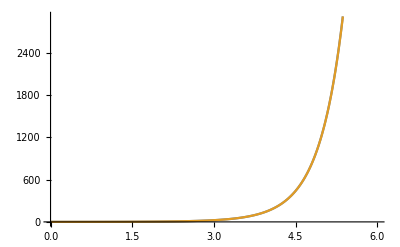

```mathematica
Block[{ΘMatrix,RMatrix,
transformedΘMatrix,SMatrix,TUMatrix,
x,y,PMatrix,approxSolutions},

Print["Exact solutions"];
{x[r_],y[r_]}={x[r],y[r]}//.DSolve[
{y'[r]-r x[r]==λ x[r],
-x'[r]+y[r]==λ y[r]},
{x[r],y[r]},r,
IncludeSingularSolutions->True
][[1]];

Print[
"x[r]= ", x[r],
"\ny[r]= ",y[r]
];

Print[
"x[r]= ", Series[x[r],{r,0,1}],
"\ny[r]= ",Series[y[r],{r,0,2}]
];

Print["\nAproximate solutions"];
RMatrix={{0,0},{0,0}};
ΘMatrix={{0,1-λ},{r+λ,0}};


{SMatrix,transformedΘMatrix,TUMatrix}=EDOSystemReducer[RMatrix,ΘMatrix,r];

Print["r^SMatrix= ",MatrixExp[Log[r]*SMatrix]//MatrixForm];
Print["TUMatrix= ",TUMatrix//MatrixForm];
Print["transformedΘMatrix= ",transformedΘMatrix//MatrixForm];

(*AbsoluteTiming[getPMatrix[SMatrix,transformedΘMatrix,10];]//Print;
AbsoluteTiming[getPMatrixNoRec[SMatrix,transformedΘMatrix,10];]//Print;*)
PMatrix=getPMatrixNoRec[SMatrix,transformedΘMatrix,25,r];
Print["PMatrix= ",PMatrix//MatrixForm];


approxSolutions=Simplify[TUMatrix.PMatrix.MatrixExp[Log[r]*SMatrix].{{C[1]},{C[2]}}];


Print[
{{"x[r]"},{"y[r]"}}//MatrixForm, "=", Collect[approxSolutions,r]//MatrixForm
];


Plot[
{y[r]/.{λ->.1,C[2]->1,C[1]->1},
approxSolutions[[2,1]]//.{λ->.1,C[2]->(AiryAiPrime[((1-λ) λ)/(1-λ)^(2/3)] a)/(1-λ)^(2/3)+(AiryBiPrime[((1-λ) λ)/(1-λ)^(2/3)] b)/(1-λ)^(2/3),C[1]-> AiryAi[((1-λ) λ)/(1-λ)^(2/3)] a+AiryBi[((1-λ) λ)/(1-λ)^(2/3)] b,a->1,b->1}
},
{r,0,6}
]


]
```

### General interior static LRSII spacetime (Static frame)

```mathematica
Block[{ΘMatrix,RMatrix,A0,ϕ0,p0,μ0,M,r0,C2,v2,
SMatrix,transformedΘMatrix,TUMatrix,PMatrix,Solutions,
Θ11,Θ12,Θ21,Θ22,rules},

RMatrix={{0,0},{0,-2}};
ΘMatrix={
{Θ11[r],Θ12[r]},
{Θ21[r],Θ22[r]}
};


{SMatrix,transformedΘMatrix,TUMatrix}=EDOSystemReducer[RMatrix,ΘMatrix,r];

rules={Θ11[0]->0,Θ22[0]->0,Θ12'[0]->0};

Print["r^SMatrix= ",MatrixExp[Log[r]*SMatrix//.rules]//MatrixForm];
Print["TUMatrix= ",TUMatrix//.rules//MatrixForm];
Print["transformedΘMatrix= ",transformedΘMatrix//.rules//MatrixForm];



PMatrix=getPMatrixNoRec[SMatrix,transformedΘMatrix//.rules,3,r];
Print["PMatrix= ",PMatrix//MatrixForm];

Solutions[r_]=TUMatrix.PMatrix.MatrixExp[Log[r]*SMatrix]//Simplify;
Print["\nSolutions: TUMatrix.PMatrix.r^SMatrix\n"];

Solutions[r_]=Collect[
Simplify[Solutions[r].{{C[1]},{C[2]}}//.rules],
r,Simplify
];

Print[{"Ψpdot[r]","ΨQ[r]"}//MatrixForm,"= ",Solutions[r]//MatrixForm];
Print[{"Ψpdot[r]","ΨQ[r]"}//MatrixForm,"C1->0 = ",Solutions[r]//.{C[1]->0}//MatrixForm];
]
```

r^SMatrix= (1/r^2 | 0
0 | 1/r^2)

TUMatrix= (-r Θ12[0] | r^2
1 | 0)

transformedΘMatrix= (-r Θ12[0] Θ21[r]+Θ22[r] | r^2 Θ21[r]
-(Θ12[0]+r Θ11[r] Θ12[0]-Θ12[r]+r^2 Θ12[0]^2 Θ21[r]-r Θ12[0] Θ22[r])/r^2 | Θ11[r]+r Θ12[0] Θ21[r])

PMatrix= (1+r Θ22[0]+1/2 r^2 (-Θ12[0] Θ21[0]+Θ22[0]^2+Θ22'[0])+1/18 r^3 (2 Θ11[0] Θ12[0] Θ21[0]+3 Θ22[0]^3-2 Θ21[0] Θ12'[0]-Θ12[0] (11 Θ21[0] Θ22[0]+6 Θ21'[0])+9 Θ22[0] Θ22'[0]+3 Θ22''[0]) | 1/3 r^3 Θ21[0]
r (Θ11[0]^2 Θ12[0]-Θ12[0]^2 Θ21[0]+Θ22[0] Θ12'[0]-Θ11[0] (2 Θ12[0] Θ22[0]+Θ12'[0])+Θ12[0] (Θ22[0]^2-Θ11'[0]+Θ22'[0])+Θ12''[0]/2)+1/12 r^2 (9 Θ11[0]^3 Θ12[0]+3 Θ22[0]^2 Θ12'[0]-3 Θ11'[0] Θ12'[0]-3 Θ11[0]^2 (5 Θ12[0] Θ22[0]+3 Θ12'[0])-6 Θ12[0]^2 (2 Θ21[0] Θ22[0]+Θ21'[0])+3 Θ12'[0] Θ22'[0]+3 Θ22[0] Θ12''[0]+3 Θ11[0] (2 Θ22[0] Θ12'[0]+Θ12[0] (Θ22[0]^2-Θ11'[0]+Θ22'[0])+Θ12''[0])+3 Θ12[0] (Θ22[0]^3-3 Θ22[0] Θ11'[0]-2 Θ21[0] Θ12'[0]+3 Θ22[0] Θ22'[0]-Θ11''[0]+Θ22''[0])+Θ12^(3)[0])+1/216 r^3 (66 Θ11[0]^4 Θ12[0]-36 Θ12[0]^3 Θ21[0]^2+12 Θ22[0]^3 Θ12'[0]+72 Θ22[0] Θ11'[0] Θ12'[0]-16 Θ21[0] Θ12'[0]^2-6 Θ11[0]^3 (17 Θ12[0] Θ22[0]+11 Θ12'[0])+36 Θ22[0] Θ12'[0] Θ22'[0]-12 Θ12'[0] Θ11''[0]+18 Θ22[0]^2 Θ12''[0]+36 Θ11'[0] Θ12''[0]+18 Θ22'[0] Θ12''[0]+2 Θ11[0]^2 (46 Θ12[0]^2 Θ21[0]+9 Θ12[0] (Θ22[0]^2+5 Θ11'[0]+Θ22'[0])+9 (2 Θ22[0] Θ12'[0]+Θ12''[0]))-4 Θ12[0]^2 (Θ21[0] (4 Θ22[0]^2+27 Θ11'[0])+30 Θ22[0] Θ21'[0]+9 Θ21''[0])+12 Θ12'[0] Θ22''[0]+12 Θ22[0] Θ12^(3)[0]-2 Θ11[0] (Θ12[0]^2 (92 Θ21[0] Θ22[0]-6 Θ21'[0])+Θ12[0] (-3 Θ22[0]^3+117 Θ22[0] Θ11'[0]+56 Θ21[0] Θ12'[0]-9 Θ22[0] Θ22'[0]+3 Θ11''[0]-3 Θ22''[0])-3 (3 Θ22[0]^2 Θ12'[0]-21 Θ11'[0] Θ12'[0]+3 Θ12'[0] Θ22'[0]+3 Θ22[0] Θ12''[0]+Θ12^(3)[0]))+2 Θ12[0] (6 Θ22[0]^4+18 Θ22[0]^2 (Θ11'[0]+2 Θ22'[0])+2 Θ22[0] (Θ21[0] Θ12'[0]-12 Θ11''[0]+12 Θ22''[0])+3 (-12 Θ11'[0]^2-8 Θ12'[0] Θ21'[0]+6 Θ11'[0] Θ22'[0]+6 Θ22'[0]^2+3 Θ21[0] Θ12''[0]-2 Θ11^(3)[0]+2 Θ22^(3)[0]))+3 Θ12^(4)[0]) | 1+r Θ11[0]+1/2 r^2 (Θ11[0]^2+Θ12[0] Θ21[0]+Θ11'[0])+1/18 r^3 (3 Θ11[0]^3+Θ11[0] (7 Θ12[0] Θ21[0]+9 Θ11'[0])+2 Θ21[0] Θ12'[0]+2 Θ12[0] (Θ21[0] Θ22[0]+3 Θ21'[0])+3 Θ11''[0]))

Solutions: TUMatrix.PMatrix.r^SMatrix

(Ψpdot[r]
ΨQ[r])= (C[2]-(C[1] Θ12[0])/r+1/2 r C[1] (-Θ12[0]^2 Θ21[0]+Θ12[0] (-2 Θ11'[0]+Θ22'[0])+Θ12''[0])+1/12 r^2 (2 C[2] (Θ12[0] Θ21[0]+3 Θ11'[0])+C[1] (-2 Θ12[0]^2 Θ21'[0]+Θ12[0] (-3 Θ11''[0]+Θ22''[0])+Θ12^(3)[0]))+1/72 r^3 (12 C[2] (2 Θ12[0] Θ21'[0]+Θ11''[0])+C[1] (-12 Θ12[0]^3 Θ21[0]^2+12 Θ11'[0] Θ12''[0]+6 Θ22'[0] Θ12''[0]-12 Θ12[0]^2 (3 Θ21[0] Θ11'[0]+Θ21''[0])+2 Θ12[0] (-12 Θ11'[0]^2+6 Θ11'[0] Θ22'[0]+6 Θ22'[0]^2+3 Θ21[0] Θ12''[0]-2 Θ11^(3)[0]+2 Θ22^(3)[0])+Θ12^(4)[0]))
C[1]/r^2+1/2 C[1] (-Θ12[0] Θ21[0]+Θ22'[0])+1/6 r (2 C[2] Θ21[0]+C[1] (-2 Θ12[0] Θ21'[0]+Θ22''[0])))

(Ψpdot[r]
ΨQ[r])C1->0 = (C[2]+1/6 r^2 C[2] (Θ12[0] Θ21[0]+3 Θ11'[0])+1/6 r^3 C[2] (2 Θ12[0] Θ21'[0]+Θ11''[0])
1/3 r C[2] Θ21[0])

### Interior Schwarzschild (static frame)

```mathematica
Block[{ΘMatrix,RMatrix,A0,ϕ0,p0,μ0,M,r0,C2,v2,σ,a,
transformedΘMatrix,SMatrix,TUMatrix,Solutions,PMatrix,
Ψpdot,ΨQ},


A0[r_]=(2M r)/(r0^3(3 √(1-(2M)/r0)-√(1-(2M)/r0^3 r^2)));
ϕ0[r_]=2/r √(1-(2M)/r0^3 r^2);
μ0=(6M)/r0^3;
p0[r_]=(μ0(√(3-μ0 r0^2)-√(3-μ0 r^2)))/(√(3-μ0 r^2)-3 √(3-μ0 r0^2));
(*a=√(1-1/3 μ0 r0^2)*)

(*A0[r_]=(μ0 r)/(3(3a-√(1-1/3 μ0 r^2)));
ϕ0[r_]=2/r √(1-1/3 μ0 r^2);

p0[r_]=(μ0(a -√(1-1/3 μ0 r^2)))/(√(1-1/3 μ0 r^2)-3a);*)
(*Print["p≈ ",Series[p0[r],{r,0,2}]];*)

v2[r_]=σ^2 Exp[Integrate[-(4A0[r])/(r ϕ0[r]),r]];


RMatrix={{0,0},{0,-2}};
ΘMatrix={
{-2/(r ϕ0[r])((μ0+p0[r])/ϕ0[r]+2A0[r]+A0[r]/C2),2/(r ϕ0[r])((μ0+p0[r])/ϕ0[r](1/2 ϕ0[r]+2A0[r])+A0[r]^2/C2+v2[r])},
{-2/(r C2 ϕ0[r]),2/(r ϕ0[r])((μ0+p0[r])/ϕ0[r]+A0[r]/C2-2A0[r])}
};


{SMatrix,transformedΘMatrix,TUMatrix}=EDOSystemReducer[RMatrix,ΘMatrix,r];

Print["r^SMatrix= ",MatrixExp[Log[r]*SMatrix]//MatrixForm];
Print["TUMatrix= ",TUMatrix//MatrixForm];
(*Print["transformedΘMatrix= ",transformedΘMatrix//Simplify//MatrixForm];*)

PMatrix=getPMatrixNoRec[SMatrix,transformedΘMatrix,1,r];
Print["PMatrix= ",PMatrix//MatrixForm];

Solutions[r_]=TUMatrix.PMatrix.MatrixExp[Log[r]*SMatrix](*//Simplify*);
Print["\nSolutions: TUMatrix.PMatrix.r^SMatrix\n"];
a=√(1-1/3 μ0 r0^2);
Solutions[r_]=Collect[
Simplify[Solutions[r].{{C[1]},{C[2]}}],
r,Simplify
];

Print[{"Ψpdot[r]","ΨQ[r]"}//MatrixForm,"= ",Solutions[r]//MatrixForm];
Print[{"Ψpdot[r]","ΨQ[r]"}//MatrixForm,"C_1→0 = ",Solutions[r]//.{C[1]->0}//MatrixForm];


]
```

r^SMatrix= (1/r^2 | 0
0 | 1/r^2)

TUMatrix= (r (-36 M^4-6 M^3 (-3+√(1-(2 M)/r0)) r0+r0^4 σ^2) | r^2
-(M-3 M √(1-(2 M)/r0))^2 r0^4 | 0)

PMatrix= (1 | 0
(r (648 (2+5 C2) M^8+36 M^7 (-32+C2 (-91+24 √(1-(2 M)/r0))) r0+4 M^6 (64+C2 (207-105 √(1-(2 M)/r0))) r0^2-18 (4+5 C2) M^4 r0^4 σ^2+8 M^3 (4+C2 (6-3 √(1-(2 M)/r0))) r0^5 σ^2+r0^8 σ^4))/(2 C2 M^2 r0^3 (9 M+(-5+3 √(1-(2 M)/r0)) r0)) | 1)

Solutions: TUMatrix.PMatrix.r^SMatrix

(Ψpdot[r]
ΨQ[r])= (((-36 M^4-6 M^3 (-3+√(1-(2 M)/r0)) r0+r0^4 σ^2) C[1])/r+(r (648 (2+5 C2) M^8+36 M^7 (-32+C2 (-91+24 √(1-(2 M)/r0))) r0+4 M^6 (64+C2 (207-105 √(1-(2 M)/r0))) r0^2-18 (4+5 C2) M^4 r0^4 σ^2+8 M^3 (4+C2 (6-3 √(1-(2 M)/r0))) r0^5 σ^2+r0^8 σ^4) C[1])/(2 C2 M^2 r0^3 (9 M+(-5+3 √(1-(2 M)/r0)) r0))+C[2]
-((M-3 M √(1-(2 M)/r0))^2 r0^4 C[1])/r^2)

(Ψpdot[r]
ΨQ[r])C_1→0 = (C[2]
0)

## Aplications 3x3

### Test1

```mathematica
Block[{ΘMatrix,RMatrix,
transformedΘMatrix,SMatrix,TUMatrix,
x,y,z,PMatrix,approxSolutions},

Print["Exact solutions"];
{x[r_],y[r_],z[r_]}={x[r],y[r],z[r]}//.DSolve[
{x'[r]==-1/r x[r]+3x[r],
y'[r]==2/r y[r]-y[r],
z'[r]==-3/r z[r]+z[r]},
{x[r],y[r],z[r]},r,
IncludeSingularSolutions->True
][[1]];

Print[
"x[r]= ", x[r],
"\ny[r]= ",y[r],
"\nz[r]= ",z[r]
];

Print[
"x[r]= ", Series[x[r],{r,0,5}],
"\ny[r]= ",Series[y[r],{r,0,8}],
"\nz[r]= ",Series[z[r],{r,0,3}]
];


Print["\nAproximate solutions"];
RMatrix={{-1,0,0},{0,2,0},{0,0,-3}};
ΘMatrix={{3,0,0},{0,-1,0},{0,0,1}};


{SMatrix,transformedΘMatrix,TUMatrix}=EDOSystemReducer[RMatrix,ΘMatrix,r];
Print["SMatrix= ",SMatrix//MatrixForm];
Print["r^SMatrix= ",MatrixExp[Log[r]*SMatrix]//MatrixForm];

PMatrix=getPMatrixNoRec[SMatrix,transformedΘMatrix,6,r];
Print["PMatrix= ",PMatrix//MatrixForm];

approxSolutions=Simplify[TUMatrix.PMatrix.MatrixExp[Log[r]*SMatrix].{{C[1]},{C[2]},{C[3]}}];

(*x2[r_]=C[1]*Part[ TUMatrix.PMatrix.MatrixExp[Log[r]*SMatrix],1,1]+C[2]* Part[TUMatrix.PMatrix.MatrixExp[Log[r]*SMatrix],1,2];
y2[r_]=C[1]*Part[ TUMatrix.PMatrix.MatrixExp[Log[r]*SMatrix],2,1]+C[2]* Part[TUMatrix.PMatrix.MatrixExp[Log[r]*SMatrix],2,2];
y2[r_]=C[1]*Part[ TUMatrix.PMatrix.MatrixExp[Log[r]*SMatrix],3,1]+C[2]* Part[TUMatrix.PMatrix.MatrixExp[Log[r]*SMatrix],2,2];*)

Print[
{{"x[r]"},{"y[r]"},{"z[r]"}}//MatrixForm, "=", Collect[approxSolutions,r]//MatrixForm
];


]
```

Exact solutions

x[r]= (ⅇ^(3 r) C[1])/r
y[r]= ⅇ^-r r^2 C[2]
z[r]= (ⅇ^r C[3])/r^3

x[r]= C[1]/r+3 C[1]+(9 C[1] r)/2+(9 C[1] r^2)/2+(27 C[1] r^3)/8+(81 C[1] r^4)/40+(81 C[1] r^5)/80+O[r]^6
y[r]= C[2] r^2-C[2] r^3+(C[2] r^4)/2-(C[2] r^5)/6+(C[2] r^6)/24-(C[2] r^7)/120+(C[2] r^8)/720+O[r]^9
z[r]= C[3]/r^3+C[3]/r^2+C[3]/(2 r)+C[3]/6+(C[3] r)/24+(C[3] r^2)/120+(C[3] r^3)/720+O[r]^4

Aproximate solutions

SMatrix= (-3 | 0 | 0
0 | -3 | 0
0 | 0 | -3)

r^SMatrix= (1/r^3 | 0 | 0
0 | 1/r^3 | 0
0 | 0 | 1/r^3)

PMatrix= (1+3 r+(9 r^2)/2+(9 r^3)/2+(27 r^4)/8+(81 r^5)/40+(81 r^6)/80 | 0 | 0
0 | 1+r+r^2/2+r^3/6+r^4/24+r^5/120+r^6/720 | 0
0 | 0 | 1-r+r^2/2-r^3/6+r^4/24-r^5/120+r^6/720)

(x[r]
y[r]
z[r])=(3 C[1]+C[1]/r+(9 r C[1])/2+(9 r^2 C[1])/2+(27 r^3 C[1])/8+(81 r^4 C[1])/40+(81 r^5 C[1])/80
r^2 C[3]-r^3 C[3]+(r^4 C[3])/2-(r^5 C[3])/6+(r^6 C[3])/24-(r^7 C[3])/120+(r^8 C[3])/720
C[2]/6+C[2]/r^3+C[2]/r^2+C[2]/(2 r)+(r C[2])/24+(r^2 C[2])/120+(r^3 C[2])/720)

### Test2

```mathematica
Block[{ΘMatrix,RMatrix,
transformedΘMatrix,SMatrix,TUMatrix,
x,y,z,PMatrix,approxSolutions},

Print["Exact solutions"];
{x[r_],y[r_],z[r_]}={x[r],y[r],z[r]}//.DSolve[
{x'[r]==-1/r x[r]+3 r x[r]-r y[r],
y'[r]==2/r y[r]-r y[r],
z'[r]==-3/r z[r]+z[r]},
{x[r],y[r],z[r]},r,
IncludeSingularSolutions->True
][[1]];

Print[
"x[r]= ", x[r],
"\ny[r]= ",y[r],
"\nz[r]= ",z[r]
];

Print[
"x[r]= ", Series[x[r],{r,0,3}],
"\ny[r]= ",Series[y[r],{r,0,4}],
"\nz[r]= ",Series[z[r],{r,0,3}]
];


Print["\nAproximate solutions"];
RMatrix={{-1,0,0},{0,2,0},{0,0,-3}};
ΘMatrix={{3 r,-r,0},{0,-r,0},{0,0,1}};


{SMatrix,transformedΘMatrix,TUMatrix}=EDOSystemReducer[RMatrix,ΘMatrix,r];

Print["r^SMatrix= ",MatrixExp[Log[r]*SMatrix]//MatrixForm];
Print["TUMatrix= ",TUMatrix//MatrixForm];
Print["transformedΘMatrix= ",transformedΘMatrix//MatrixForm];

PMatrix=getPMatrixNoRec[SMatrix,transformedΘMatrix,4,r];
Print["PMatrix= ",PMatrix//MatrixForm];


approxSolutions=Simplify[TUMatrix.PMatrix.MatrixExp[Log[r]*SMatrix].{{C[1]},{C[2]},{C[3]}}];
Print[
{{"x[r]"},{"y[r]"},{"z[r]"}}//MatrixForm, "=", Collect[approxSolutions,r]//MatrixForm
];


]
```

Exact solutions

x[r]= (ⅇ^((3 r^2)/2) C[2])/r+(ⅇ^((3 r^2)/2) C[1] (4 ⅇ^(-2 r^2) r (3+4 r^2)-3 √(2 π) Erf[√2 r]))/(64 r)
y[r]= ⅇ^(-r^2/2) r^2 C[1]
z[r]= (ⅇ^r C[3])/r^3

x[r]= C[2]/r+(3 C[2] r)/2+(9 C[2] r^3)/8+O[r]^4
y[r]= C[1] r^2-(C[1] r^4)/2+O[r]^5
z[r]= C[3]/r^3+C[3]/r^2+C[3]/(2 r)+C[3]/6+(C[3] r)/24+(C[3] r^2)/120+(C[3] r^3)/720+O[r]^4

Aproximate solutions

r^SMatrix= (1/r^3 | 0 | 0
0 | 1/r^3 | 0
0 | 0 | 1/r^3)

TUMatrix= (r^2 | 0 | 0
0 | 0 | r^5
0 | 1 | 0)

transformedΘMatrix= (3 r | 0 | -r^4
0 | 1 | 0
0 | 0 | -r)

PMatrix= (1+(3 r^2)/2+(9 r^4)/8 | 0 | 0
0 | 1+r+r^2/2+r^3/6+r^4/24 | 0
0 | 0 | 1-r^2/2+r^4/8)

(x[r]
y[r]
z[r])=(C[1]/r+(3 r C[1])/2+(9 r^3 C[1])/8
r^2 C[3]-(r^4 C[3])/2+(r^6 C[3])/8
C[2]/6+C[2]/r^3+C[2]/r^2+C[2]/(2 r)+(r C[2])/24)

### Test3

```mathematica
Block[{ΘMatrix,RMatrix,
transformedΘMatrix,SMatrix,TUMatrix,
x,y,z,PMatrix,approxSolutions},

Print["Exact solutions"];
{x[r_],y[r_],z[r_]}={x[r],y[r],z[r]}//.DSolve[
{x'[r]==-1/r x[r]+3 r x[r]-r y[r],
y'[r]==-2/r y[r]-r^3 y[r],
z'[r]==-2/r z[r]+z[r]},
{x[r],y[r],z[r]},r,
IncludeSingularSolutions->True
][[1]];

Print[
"x[r]= ", x[r],
"\ny[r]= ",y[r],
"\nz[r]= ",z[r]
];

Print[
"x[r]= ", Series[x[r],{r,0,8}],
"\ny[r]= ",Series[y[r],{r,0,6}],
"\nz[r]= ",Series[z[r],{r,0,5}]
];


Print["\nAproximate solutions"];
RMatrix={{-1,0,0},{0,-2,0},{0,0,-2}};
ΘMatrix={{3 r,-r,0},{0,-r^3,0},{0,0,1}};


{SMatrix,transformedΘMatrix,TUMatrix}=EDOSystemReducer[RMatrix,ΘMatrix,r];

(*Print["r^SMatrix= ",MatrixExp[Log[r]*SMatrix]//MatrixForm];
Print["TUMatrix= ",TUMatrix//MatrixForm];
Print["transformedΘMatrix= ",transformedΘMatrix//MatrixForm];*)

PMatrix=getPMatrixNoRec[SMatrix,transformedΘMatrix,10,r];
Print["PMatrix_exact= ",MatrixExp[transformedΘMatrix*r]//MatrixForm];
Print["PMatrix= ",PMatrix//MatrixForm];
(*AbsoluteTiming[getPMatrix[SMatrix,transformedΘMatrix,10];]//Print;
AbsoluteTiming[getPMatrixNoRec[SMatrix,transformedΘMatrix,10];]//Print;*)


approxSolutions=Simplify[TUMatrix.PMatrix.MatrixExp[Log[r]*SMatrix].{{C[1]},{C[2]},{C[3]}}];
Print[
{{"x[r]"},{"y[r]"},{"z[r]"}}//MatrixForm, "=", Collect[approxSolutions,r]//MatrixForm
];


]
```

Exact solutions

x[r]= (ⅇ^((3 r^2)/2) C[2])/r+(ⅇ^((3 r^2)/2) C[1] -ⅇ^(-3/2 K[1]^2-K[1]^4/4)K[1]1r)/r
y[r]= (ⅇ^(-r^4/4) C[1])/r^2
z[r]= (ⅇ^r C[3])/r^2

x[r]= (C[2]-C[1] ∫_1^0 ⅇ^(-3/2 K[1]^2-K[1]^4/4)ⅆK[1])/r-C[1]+3/2 (C[2]-C[1] ∫_1^0 ⅇ^(-3/2 K[1]^2-K[1]^4/4)ⅆK[1]) r-C[1] r^2+((9 C[2])/8-9/8 C[1] ∫_1^0 ⅇ^(-3/2 K[1]^2-K[1]^4/4)ⅆK[1]) r^3-(11 C[1] r^4)/20+((9 C[2])/16-9/16 C[1] ∫_1^0 ⅇ^(-3/2 K[1]^2-K[1]^4/4)ⅆK[1]) r^5-(33 C[1] r^6)/140+((27 C[2])/128-27/128 C[1] ∫_1^0 ⅇ^(-3/2 K[1]^2-K[1]^4/4)ⅆK[1]) r^7-(827 C[1] r^8)/10080+O[r]^9
y[r]= C[1]/r^2-(C[1] r^2)/4+(C[1] r^6)/32+O[r]^7
z[r]= C[3]/r^2+C[3]/r+C[3]/2+(C[3] r)/6+(C[3] r^2)/24+(C[3] r^3)/120+(C[3] r^4)/720+(C[3] r^5)/5040+O[r]^6

Aproximate solutions

PMatrix_exact= (ⅇ^r | 0 | 0
0 | ⅇ^(-r^4) | 0
0 | -(ⅇ^(-r^4) (-1+ⅇ^(3 r^2+r^4)))/(r (3+r^2)) | ⅇ^(3 r^2))

PMatrix= (1+r+r^2/2+r^3/6+r^4/24+r^5/120+r^6/720+r^7/5040+r^8/40320+r^9/362880+r^10/3628800 | 0 | 0
0 | 1-r^4/4+r^8/32 | 0
0 | -r-r^3-(11 r^5)/20-(33 r^7)/140-(827 r^9)/10080 | 1+(3 r^2)/2+(9 r^4)/8+(9 r^6)/16+(27 r^8)/128+(81 r^10)/1280)

(x[r]
y[r]
z[r])=(-C[2]-r^2 C[2]-(11 r^4 C[2])/20-(33 r^6 C[2])/140-(827 r^8 C[2])/10080+C[3]/r+(3 r C[3])/2+(9 r^3 C[3])/8+(9 r^5 C[3])/16+(27 r^7 C[3])/128+(81 r^9 C[3])/1280
C[2]/r^2-(r^2 C[2])/4+(r^6 C[2])/32
C[1]/2+C[1]/r^2+C[1]/r+(r C[1])/6+(r^2 C[1])/24+(r^3 C[1])/120+(r^4 C[1])/720+(r^5 C[1])/5040+(r^6 C[1])/40320+(r^7 C[1])/362880+(r^8 C[1])/3628800)

### General case (Comoving frame)

```mathematica
Block[{ΘMatrix,RMatrix,A0,ϕ0,p0,μ0,M,r0,C2,v2,Ε0,σ,γ,
transformedΘMatrix,SMatrix,TUMatrix,Solutions,PMatrix,
Θ11,Θ12,Θ13,Θ21,Θ22,Θ23,Θ31,Θ32,Θ33,rules},


RMatrix={{0,0,0},{0,1,0},{0,0,-3}};
ΘMatrix={
{Θ11[r],Θ12[r],Θ13[r]},
{Θ21[r],Θ22[r],Θ23[r]},
{Θ31[r],Θ32[r],Θ33[r]}
};


{SMatrix,transformedΘMatrix,TUMatrix}=EDOSystemReducer[RMatrix,ΘMatrix,r];

rules={Θ11[0]->0,Θ13[0]->0,Θ21[0]->0,Θ22[0]->0,Θ31[0]->0,Θ33[0]->0,
Θ12'[0]->0,Θ21'[0]->0,Θ23'[0]->0,Θ32'[0]->0,
Θ13''[0]->0,Θ22''[0]->0,Θ33''[0]->0,
Θ23'''[0]->0};

SMatrix=Simplify[SMatrix//.rules];
transformedΘMatrix=Simplify[transformedΘMatrix//.rules];
TUMatrix=Simplify[TUMatrix//.rules];

Print["r^SMatrix= ",MatrixExp[Log[r]*SMatrix]//MatrixForm];
Print["TUMatrix= ",TUMatrix//MatrixForm];
Print["transformedΘMatrix= ",Collect[transformedΘMatrix//Simplify,r]//MatrixForm];

PMatrix=getPMatrixNoRec[SMatrix,transformedΘMatrix,2,r];
Print["PMatrix= ",PMatrix//MatrixForm];


Solutions[r_]=TUMatrix.PMatrix.MatrixExp[Log[r]*SMatrix];
Print["\nSolutions: TUMatrix.PMatrix.r^SMatrix\n"];
Solutions[r_]=Collect[
Simplify[Solutions[r].{{C[1]},{C[2]},{C[3]}}//.rules],
r
];

Print[{"Ψṗ[r]","ΨȦ[r]","ΨΣ[r]"}//MatrixForm,"= ",Solutions[r]//MatrixForm];
Print[{"Ψṗ[r]","ΨȦ[r]","ΨΣ[r]"}//MatrixForm,"C_2→0 = ",Solutions[r]//.{C[2]->0}//MatrixForm];

]
```

r^SMatrix= (1/r^3 | 0 | 0
0 | 1/r^3 | 0
0 | 0 | 1/r^3)

TUMatrix= (-r^3 | 12 r^2 (Θ12[0] Θ23[0]-3 Θ13'[0]) | 0
0 | -12 r Θ23[0]+2 r^3 (2 Θ23[0]^2 Θ32[0]+6 Θ23[0] (Θ22'[0]-Θ33'[0])-9 Θ23''[0]) | r^4
0 | 36 | 0)

transformedΘMatrix= (Θ11[r]-1/3 r^2 Θ31[r] (Θ12[0] Θ23[0]-3 Θ13'[0]) | -(36 Θ13[r])/r^3+(2 (18 Θ12[r] Θ23[0]-18 (Θ12[0] Θ23[0]-3 Θ13'[0])))/(3 r^2)+(2 (-18 Θ11[r] (Θ12[0] Θ23[0]-3 Θ13'[0])+18 Θ33[r] (Θ12[0] Θ23[0]-3 Θ13'[0])))/(3 r)+4 r Θ31[r] (Θ12[0] Θ23[0]-3 Θ13'[0])^2+2/3 r^2 Θ32[r] (Θ12[0] Θ23[0]-3 Θ13'[0]) (2 Θ23[0]^2 Θ32[0]+6 Θ23[0] (Θ22'[0]-Θ33'[0])-9 Θ23''[0])+2/3 (-6 Θ12[r] Θ23[0]^2 Θ32[0]-6 Θ23[0] Θ32[r] (Θ12[0] Θ23[0]-3 Θ13'[0])-18 Θ12[r] Θ23[0] (Θ22'[0]-Θ33'[0])+27 Θ12[r] Θ23''[0]) | -r Θ12[r]+1/3 r^3 Θ32[r] (Θ12[0] Θ23[0]-3 Θ13'[0])
-1/36 r^3 Θ31[r] | -1/3 r Θ23[0] Θ32[r]+Θ33[r]+1/3 r^2 Θ31[r] (Θ12[0] Θ23[0]-3 Θ13'[0])+1/18 r^3 Θ32[r] (2 Θ23[0]^2 Θ32[0]+6 Θ23[0] (Θ22'[0]-Θ33'[0])-9 Θ23''[0]) | 1/36 r^4 Θ32[r]
-Θ21[r]/r-1/3 Θ23[0] Θ31[r]+r^2 (1/9 Θ23[0]^2 Θ31[r] Θ32[0]+1/3 Θ23[0] Θ31[r] (Θ22'[0]-Θ33'[0])-1/2 Θ31[r] Θ23''[0]) | -(1296 Θ23[0]-1296 Θ23[r])/(36 r^4)-(432 Θ22[r] Θ23[0]-432 Θ23[0] Θ33[r])/(36 r^3)-(144 Θ23[0]^2 Θ32[r]-432 Θ21[r] (Θ12[0] Θ23[0]-3 Θ13'[0])-72 (2 Θ23[0]^2 Θ32[0]+6 Θ23[0] (Θ22'[0]-Θ33'[0])-9 Θ23''[0]))/(36 r^2)-(-144 Θ23[0] Θ31[r] (Θ12[0] Θ23[0]-3 Θ13'[0])-72 Θ22[r] (2 Θ23[0]^2 Θ32[0]+6 Θ23[0] (Θ22'[0]-Θ33'[0])-9 Θ23''[0])+72 Θ33[r] (2 Θ23[0]^2 Θ32[0]+6 Θ23[0] (Θ22'[0]-Θ33'[0])-9 Θ23''[0]))/(36 r)+4/3 Θ23[0] Θ32[r] (2 Θ23[0]^2 Θ32[0]+6 Θ23[0] (Θ22'[0]-Θ33'[0])-9 Θ23''[0])-2/3 r Θ31[r] (Θ12[0] Θ23[0]-3 Θ13'[0]) (2 Θ23[0]^2 Θ32[0]+6 Θ23[0] (Θ22'[0]-Θ33'[0])-9 Θ23''[0])-1/36 r^2 (8 Θ23[0]^2 Θ32[0] Θ32[r] (2 Θ23[0]^2 Θ32[0]+6 Θ23[0] (Θ22'[0]-Θ33'[0])-9 Θ23''[0])+24 Θ23[0] Θ32[r] (Θ22'[0]-Θ33'[0]) (2 Θ23[0]^2 Θ32[0]+6 Θ23[0] (Θ22'[0]-Θ33'[0])-9 Θ23''[0])-36 Θ32[r] (2 Θ23[0]^2 Θ32[0]+6 Θ23[0] (Θ22'[0]-Θ33'[0])-9 Θ23''[0]) Θ23''[0]) | Θ22[r]+1/3 r Θ23[0] Θ32[r]+r^3 (-1/9 Θ23[0]^2 Θ32[0] Θ32[r]-1/3 Θ23[0] Θ32[r] (Θ22'[0]-Θ33'[0])+1/2 Θ32[r] Θ23''[0]))

PMatrix= (1+r Θ11[0]+1/2 r^2 (Θ11[0]^2+Θ11'[0]) | r (-2 Θ12[0] (4 Θ23[0]^2 Θ32[0]+6 Θ23[0] (Θ11'[0]+Θ22'[0]-2 Θ33'[0])-9 Θ23''[0])+6 (6 Θ11'[0] Θ13'[0]-6 Θ13'[0] Θ33'[0]+Θ23[0] (2 Θ32[0] Θ13'[0]+Θ12''[0])-Θ13^(3)[0]))+r^2 (2 Θ12[0]^2 Θ23[0]^2 Θ31[0]-2 Θ23[0]^2 Θ32[0] Θ12'[0]+18 Θ31[0] Θ13'[0]^2+9 Θ13'[0] Θ11''[0]+9 Θ12'[0] Θ23''[0]-Θ12[0] (2 Θ23[0]^2 (2 Θ32[0] Θ33[0]+Θ32'[0])+Θ11[0] (4 Θ23[0]^2 Θ32[0]+6 Θ23[0] (Θ11'[0]+Θ22'[0]-2 Θ33'[0])-9 Θ23''[0])-9 Θ33[0] Θ23''[0]+3 Θ23[0] (4 Θ31[0] Θ13'[0]+2 Θ33[0] (Θ11'[0]+Θ22'[0]-2 Θ33'[0])+Θ11''[0]-Θ33''[0]))-9 Θ13'[0] Θ33''[0]+Θ23[0] (6 Θ32[0] Θ33[0] Θ13'[0]-6 Θ12'[0] Θ22'[0]+6 Θ13'[0] Θ32'[0]+6 Θ12'[0] Θ33'[0]+3 Θ33[0] Θ12''[0]+3 Θ11[0] (2 Θ32[0] Θ13'[0]+Θ12''[0])+Θ12^(3)[0])+3 Θ11[0] (6 Θ11'[0] Θ13'[0]-6 Θ13'[0] Θ33'[0]-Θ13^(3)[0])+3 Θ33[0] (6 Θ11'[0] Θ13'[0]-6 Θ13'[0] Θ33'[0]-Θ13^(3)[0])-3/4 Θ13^(4)[0]) | -1/2 r^2 Θ12[0]
0 | 1+r Θ33[0]+1/6 r^2 (-Θ23[0] Θ32[0]+3 (Θ33[0]^2+Θ33'[0])) | 0
r (-1/3 Θ23[0] Θ31[0]-Θ21'[0])+1/12 r^2 (-2 Θ11[0] (Θ23[0] Θ31[0]+3 Θ21'[0])-2 Θ22[0] (Θ23[0] Θ31[0]+3 Θ21'[0])-2 Θ23[0] Θ31'[0]-3 Θ21''[0]) | r (8/3 Θ23[0]^3 Θ32[0]^2-18 Θ13'[0] Θ21''[0]-18 Θ22'[0] Θ23''[0]+18 Θ33'[0] Θ23''[0]+2 Θ23[0]^2 (2 Θ12[0] Θ31'[0]+6 Θ32[0] (Θ22'[0]-Θ33'[0])-Θ32''[0])+2 Θ23[0] (6 Θ22'[0]^2-6 Θ13'[0] Θ31'[0]-12 Θ22'[0] Θ33'[0]+6 Θ33'[0]^2+3 Θ12[0] Θ21''[0]-6 Θ32[0] Θ23''[0]-Θ22^(3)[0]+Θ33^(3)[0])+3/2 Θ23^(4)[0])+r^2 (2/3 Θ12[0] Θ23[0]^3 Θ31[0] Θ32[0]+4/3 Θ22[0] Θ23[0]^3 Θ32[0]^2+4/3 Θ23[0]^3 Θ32[0]^2 Θ33[0]-6 Θ23[0] Θ31[0] Θ11'[0] Θ13'[0]-6 Θ23[0] Θ32[0] Θ13'[0] Θ21'[0]-18 Θ11'[0] Θ13'[0] Θ21'[0]+6 Θ23[0]^2 Θ32[0] Θ33[0] Θ22'[0]+6 Θ23[0] Θ31[0] Θ13'[0] Θ22'[0]+6 Θ23[0] Θ33[0] Θ22'[0]^2-6 Θ23[0] Θ33[0] Θ13'[0] Θ31'[0]+4/3 Θ23[0]^3 Θ32[0] Θ32'[0]+4 Θ23[0]^2 Θ22'[0] Θ32'[0]-6 Θ23[0]^2 Θ32[0] Θ33[0] Θ33'[0]+18 Θ13'[0] Θ21'[0] Θ33'[0]-12 Θ23[0] Θ33[0] Θ22'[0] Θ33'[0]-4 Θ23[0]^2 Θ32'[0] Θ33'[0]+6 Θ23[0] Θ33[0] Θ33'[0]^2-Θ23[0]^2 Θ31[0] Θ12''[0]-3 Θ23[0] Θ21'[0] Θ12''[0]-9 Θ33[0] Θ13'[0] Θ21''[0]+Θ23[0]^2 Θ32[0] Θ22''[0]+3 Θ23[0] Θ22'[0] Θ22''[0]-3 Θ23[0] Θ33'[0] Θ22''[0]-6 Θ23[0] Θ32[0] Θ33[0] Θ23''[0]-9 Θ31[0] Θ13'[0] Θ23''[0]-9 Θ12[0] Θ21'[0] Θ23''[0]-9 Θ33[0] Θ22'[0] Θ23''[0]-6 Θ23[0] Θ32'[0] Θ23''[0]+9 Θ33[0] Θ33'[0] Θ23''[0]-9/2 Θ22''[0] Θ23''[0]-3 Θ23[0] Θ13'[0] Θ31''[0]+Θ12[0] Θ23[0]^2 (4 Θ32[0] Θ21'[0]+2 Θ22[0] Θ31'[0]+2 Θ33[0] Θ31'[0]+2 Θ31[0] (Θ11'[0]-Θ33'[0])+Θ31''[0])+Θ22[0] Θ23[0]^2 (6 Θ32[0] (Θ22'[0]-Θ33'[0])-Θ32''[0])-Θ23[0]^2 Θ33[0] Θ32''[0]-Θ23[0]^2 Θ32[0] Θ33''[0]-3 Θ23[0] Θ22'[0] Θ33''[0]+3 Θ23[0] Θ33'[0] Θ33''[0]+9/2 Θ23''[0] Θ33''[0]+Θ23[0] Θ31[0] Θ13^(3)[0]+3 Θ21'[0] Θ13^(3)[0]-3 Θ13'[0] Θ21^(3)[0]+Θ12[0] Θ23[0] (6 Θ11'[0] Θ21'[0]+6 Θ21'[0] (Θ22'[0]-2 Θ33'[0])+3 Θ22[0] Θ21''[0]+3 Θ33[0] Θ21''[0]+Θ21^(3)[0])-Θ23[0] Θ33[0] Θ22^(3)[0]-1/3 Θ23[0]^2 Θ32^(3)[0]+Θ23[0] Θ33[0] Θ33^(3)[0]+Θ22[0] Θ23[0] (6 Θ22'[0]^2-6 Θ13'[0] Θ31'[0]-12 Θ22'[0] Θ33'[0]+6 Θ33'[0]^2-6 Θ32[0] Θ23''[0]-Θ22^(3)[0]+Θ33^(3)[0])-1/4 Θ23[0] Θ22^(4)[0]+3/4 Θ33[0] Θ23^(4)[0]+3/4 Θ22[0] (-12 Θ13'[0] Θ21''[0]-12 Θ22'[0] Θ23''[0]+12 Θ33'[0] Θ23''[0]+Θ23^(4)[0])+1/4 Θ23[0] Θ33^(4)[0]+3/20 Θ23^(5)[0]) | 1+r Θ22[0]+1/6 r^2 (3 Θ22[0]^2+Θ23[0] Θ32[0]+3 Θ22'[0]))

Solutions: TUMatrix.PMatrix.r^SMatrix

(Ψṗ[r]
ΨȦ[r]
ΨΣ[r])= (-C[1]+(12 C[2] (Θ12[0] Θ23[0]-3 Θ13'[0]))/r+6 r C[2] (-6 Θ11'[0] Θ13'[0]+3 Θ13'[0] Θ33'[0]-Θ23[0] (Θ32[0] Θ13'[0]+Θ12''[0])+Θ12[0] (Θ23[0]^2 Θ32[0]+Θ23[0] (2 Θ11'[0]+2 Θ22'[0]-3 Θ33'[0])-3 Θ23''[0])+Θ13^(3)[0])+1/4 r^2 (2 C[3] Θ12[0]-2 C[1] Θ11'[0]+C[2] (12 Θ12[0] Θ23[0] Θ11''[0]-36 Θ13'[0] Θ11''[0]-4 Θ23[0] Θ12^(3)[0]+3 Θ13^(4)[0]))
r C[3]-(12 C[2] Θ23[0])/r^2+6 C[2] (Θ23[0]^2 Θ32[0]+Θ23[0] (2 Θ22'[0]-3 Θ33'[0])-3 Θ23''[0])+1/2 r^2 C[2] (4 Θ23[0]^3 Θ32[0]^2+4 Θ23[0]^2 (2 Θ12[0] Θ31'[0]+Θ32[0] (5 Θ22'[0]-4 Θ33'[0])-Θ32''[0])+2 Θ23[0] (12 Θ22'[0]^2-12 Θ13'[0] Θ31'[0]-18 Θ22'[0] Θ33'[0]+6 Θ33'[0]^2+6 Θ12[0] Θ21''[0]-9 Θ32[0] Θ23''[0]-2 Θ22^(3)[0]+2 Θ33^(3)[0])+3 (-12 Θ13'[0] Θ21''[0]-12 Θ22'[0] Θ23''[0]+6 Θ33'[0] Θ23''[0]+Θ23^(4)[0]))+1/60 r^3 (10 C[3] (Θ23[0] Θ32[0]+3 Θ22'[0])-5 C[1] (2 Θ23[0] Θ31'[0]+3 Θ21''[0])+C[2] (60 Θ12[0] Θ23[0] (Θ23[0] Θ31''[0]+Θ21^(3)[0])-20 Θ23[0]^2 Θ32^(3)[0]-15 Θ23[0] (12 Θ13'[0] Θ31''[0]+Θ22^(4)[0]-Θ33^(4)[0])+9 (-20 Θ13'[0] Θ21^(3)[0]+Θ23^(5)[0])))
(36 C[2])/r^3-(6 C[2] (Θ23[0] Θ32[0]-3 Θ33'[0]))/r)

(Ψṗ[r]
ΨȦ[r]
ΨΣ[r])C_2→0 = (-C[1]+1/4 r^2 (2 C[3] Θ12[0]-2 C[1] Θ11'[0])
r C[3]+1/60 r^3 (10 C[3] (Θ23[0] Θ32[0]+3 Θ22'[0])-5 C[1] (2 Θ23[0] Θ31'[0]+3 Θ21''[0]))
0)

### Interior Schwarzschild (Comoving frame)

```mathematica
Block[{ΘMatrix,RMatrix,A0,ϕ0,p0,μ0,Ε0,M,r0,C2,v2,σ,
transformedΘMatrix,SMatrix,TUMatrix,PMatrix,Solutions,
t0},

A0[r_]=(2M r)/(r0^3(3 √(1-(2M)/r0)-√(1-(2M)/r0^3 r^2)));
ϕ0[r_]=2/r √(1-(2M)/r0^3 r^2);
μ0=(6M)/r0^3;
p0[r_]=(μ0(√(3-μ0 r0^2)-√(3-μ0 r^2)))/(√(3-μ0 r^2)-3 √(3-μ0 r0^2));

(*Ε0[r_]=1/3(μ0[r]+3p0[r])-A0[r]ϕ0[r];*)
Ε0[r_]=0;

v2[r_]=σ^2 Exp[Integrate[-(4A0[r])/(r ϕ0[r]),r]];



RMatrix={{0,0,0},{0,1,0},{0,0,-3}};
ΘMatrix=2/(r ϕ0[r])*{
{-2A0[r](1+1/(3C2)),
-(μ0+p0[r]),

-(μ0+p0[r])A0[r]},
{Ε0[r]/(C2(μ0+p0[r])),
-3 A0[r],
-3/2(v2[r]+A0[r]^2+1/3 μ0-2Ε0[r])
},
{(4A0[r])/(9(μ0+p0[r])C2^2)+(2A0[r](μ0+p0[r]))/(3(μ0+p0[r])^2 C2),
2/(3 C2),
(2 A0[r])/(3C2)
}
}//Simplify;

{SMatrix,transformedΘMatrix,TUMatrix}=EDOSystemReducer[RMatrix,ΘMatrix,r];
Print["r^SMatrix= ",MatrixExp[Log[r]*SMatrix]//MatrixForm];
Print["TUMatrix= ",TUMatrix//MatrixForm];
(*Print["transformedΘMatrix= ",transformedΘMatrix//MatrixForm];*)

PMatrix=getPMatrixNoRec[SMatrix,transformedΘMatrix,2,r];

Solutions[r_]=TUMatrix.PMatrix.MatrixExp[Log[r]*SMatrix];
Print["\nSolutions: TUMatrix.PMatrix.r^SMatrix\n"];
SetOptions[Simplify,TimeConstraint->1];

Solutions[r_]=Collect[
Simplify[Solutions[r].{{C[1]},{C[2]},{C[3]}}],
r
];


Print[{"Ψṗ[r]","ΨȦ[r]","ΨΣ[r]"}//MatrixForm,"= ",Solutions[r]//MatrixForm];

Print[{"Ψṗ[r]","ΨȦ[r]","ΨΣ[r]"}//MatrixForm,"C_2→0 = ",Solutions[r]/.{C[2]->0}//MatrixForm];

(*Set to default*)
SetOptions[Simplify,TimeConstraint->300];

]
```

r^SMatrix= (1/r^3 | 0 | 0
0 | 1/r^3 | 0
0 | 0 | 1/r^3)

TUMatrix= (r^3 | -72 C2 M^3 r^2 √(1-(2 M)/r0) (9 M+(-5+3 √(1-(2 M)/r0)) r0) (-36 M^4+16 M^3 r0+r0^4 σ^2) | 0
0 | -6 C2 M^2 r (-1+3 √(1-(2 M)/r0)) r0^3 (9 M+(-5+3 √(1-(2 M)/r0)) r0) (-36 M^4+4 M^3 (5-3 √(1-(2 M)/r0)) r0+r0^4 σ^2)+r^3 (1944 (2+9 C2) M^8 (-1+√(1-(2 M)/r0))-72 M^7 (-52+9 C2 (-29+33 √(1-(2 M)/r0))+60 √(1-(2 M)/r0)) r0+16 (8+45 C2) M^6 (-7+9 √(1-(2 M)/r0)) r0^2-18 M^4 (-8+27 C2 (-1+√(1-(2 M)/r0))+12 √(1-(2 M)/r0)) r0^4 σ^2+12 M^3 (-6+3 C2 (-7+9 √(1-(2 M)/r0))+10 √(1-(2 M)/r0)) r0^5 σ^2+(-1+3 √(1-(2 M)/r0)) r0^8 σ^4) | r^4
0 | -12 C2 M^2 (-1+3 √(1-(2 M)/r0)) (M-3 M √(1-(2 M)/r0))^2 r0^7 (9 M+(-5+3 √(1-(2 M)/r0)) r0) | 0)

Solutions: TUMatrix.PMatrix.r^SMatrix

(Ψṗ[r]
ΨȦ[r]
ΨΣ[r])= (C[1]+(-648 C2 M^4 √(1-(2 M)/r0) (-36 M^4+16 M^3 r0+r0^4 σ^2) C[2]-72 C2 M^3 (-5+3 √(1-(2 M)/r0)) √(1-(2 M)/r0) r0 (-36 M^4+16 M^3 r0+r0^4 σ^2) C[2])/r+r (-(216 M^5 √(1-(2 M)/r0) (-36 M^4+16 M^3 r0+r0^4 σ^2) C[2])/r0^3+(96 M^4 √(1-(2 M)/r0) (-36 M^4+16 M^3 r0+r0^4 σ^2) C[2])/r0^2+6 M √(1-(2 M)/r0) r0 σ^2 (-36 M^4+16 M^3 r0+r0^4 σ^2) C[2]-(24 M √(1-(2 M)/r0) (324 M^8 (-4+9 C2 (-3+4 √(1-(2 M)/r0))+12 √(1-(2 M)/r0))-36 M^7 (-32+C2 (-249+351 √(1-(2 M)/r0))+96 √(1-(2 M)/r0)) r0+128 M^6 (-2+9 C2 (-2+3 √(1-(2 M)/r0))+6 √(1-(2 M)/r0)) r0^2-9 M^4 (-8+9 C2 (-3+4 √(1-(2 M)/r0))+24 √(1-(2 M)/r0)) r0^4 σ^2+M^3 (-32+3 C2 (-41+63 √(1-(2 M)/r0))+96 √(1-(2 M)/r0)) r0^5 σ^2+(-1+3 √(1-(2 M)/r0)) r0^8 σ^4) C[2])/((-1+3 √(1-(2 M)/r0)) r0^3))+r^2 ((2 (1+3 C2) M C[1])/(3 (C2-3 C2 √(1-(2 M)/r0)) r0^3)-(6 M √(1-(2 M)/r0) C[3])/((-1+3 √(1-(2 M)/r0)) r0^3))
1944 (2+9 C2) M^8 (-1+√(1-(2 M)/r0)) C[2]-72 M^7 (-52+9 C2 (-29+33 √(1-(2 M)/r0))+60 √(1-(2 M)/r0)) r0 C[2]+16 (8+45 C2) M^6 (-7+9 √(1-(2 M)/r0)) r0^2 C[2]-18 M^4 (-8+27 C2 (-1+√(1-(2 M)/r0))+12 √(1-(2 M)/r0)) r0^4 σ^2 C[2]+12 M^3 (-6+3 C2 (-7+9 √(1-(2 M)/r0))+10 √(1-(2 M)/r0)) r0^5 σ^2 C[2]+(-1+3 √(1-(2 M)/r0)) r0^8 σ^4 C[2]-(6 C2 M^2 (-1+3 √(1-(2 M)/r0)) r0^3 (9 M+(-5+3 √(1-(2 M)/r0)) r0) (-36 M^4+4 M^3 (5-3 √(1-(2 M)/r0)) r0+r0^4 σ^2) C[2])/r^2+1/2 (-1+3 √(1-(2 M)/r0)) (-36 M^4+16 M^3 r0+r0^4 σ^2) (-36 M^4+4 M^3 (5-3 √(1-(2 M)/r0)) r0+r0^4 σ^2) C[2]+r^2 (-((-36 M^4+16 M^3 r0+r0^4 σ^2) (1944 (2+9 C2) M^8 (-1+√(1-(2 M)/r0))-72 M^7 (-52+9 C2 (-29+33 √(1-(2 M)/r0))+60 √(1-(2 M)/r0)) r0+16 (8+45 C2) M^6 (-7+9 √(1-(2 M)/r0)) r0^2-18 M^4 (-8+27 C2 (-1+√(1-(2 M)/r0))+12 √(1-(2 M)/r0)) r0^4 σ^2+12 M^3 (-6+3 C2 (-7+9 √(1-(2 M)/r0))+10 √(1-(2 M)/r0)) r0^5 σ^2+(-1+3 √(1-(2 M)/r0)) r0^8 σ^4) C[2])/(12 C2 M^2 r0^3 (9 M+(-5+3 √(1-(2 M)/r0)) r0))+(2 (26244 (16+84 C2+81 C2^2) M^13+11664 M^12 (-80+C2^2 (-351+81 √(1-(2 M)/r0))+C2 (-435+126 √(1-(2 M)/r0))+24 √(1-(2 M)/r0)) r0-1296 M^11 (-584+27 C2^2 (-80+33 √(1-(2 M)/r0))+6 C2 (-556+291 √(1-(2 M)/r0))+312 √(1-(2 M)/r0)) r0^2+288 M^10 (-928+27 C2^2 (-101+54 √(1-(2 M)/r0))+C2 (-5637+4059 √(1-(2 M)/r0))+672 √(1-(2 M)/r0)) r0^3-243 M^8 (80 (-3+√(1-(2 M)/r0))+27 C2^2 (-13+4 √(1-(2 M)/r0))+C2 (-868+288 √(1-(2 M)/r0))) r0^5 σ^2+18 M^7 (352 (-5+3 √(1-(2 M)/r0))+27 C2^2 (-79+42 √(1-(2 M)/r0))+C2 (-6624+3996 √(1-(2 M)/r0))) r0^6 σ^2+2 M^6 (2816+C2 (11100-9252 √(1-(2 M)/r0))-27 C2^2 (-97+63 √(1-(2 M)/r0))-2304 √(1-(2 M)/r0)) r0^7 σ^2+243 (4+7 C2) M^5 r0^8 σ^4+54 M^4 (-20+C2 (-36+15 √(1-(2 M)/r0))+8 √(1-(2 M)/r0)) r0^9 σ^4+2 M^3 (148+C2 (273-207 √(1-(2 M)/r0))-108 √(1-(2 M)/r0)) r0^10 σ^4-9 M r0^12 σ^6+(5-3 √(1-(2 M)/r0)) r0^13 σ^6-M^9 r0^4 (-34816+30720 √(1-(2 M)/r0)+34992 σ^2+27 C2^2 (-2656+1440 √(1-(2 M)/r0)+2187 σ^2)+24 C2 (-9472+8448 √(1-(2 M)/r0)+5103 σ^2))) C[2])/(3 C2 M^2 (-1+3 √(1-(2 M)/r0)) r0^4 (9 M+(-5+3 √(1-(2 M)/r0)) r0)))+r C[3]+r^3 (-((2+3 C2) (324 M^5 (-5+3 √(1-(2 M)/r0))-72 M^4 (-25+21 √(1-(2 M)/r0)) r0+16 M^3 (-31+33 √(1-(2 M)/r0)) r0^2-27 M (-1+√(1-(2 M)/r0)) r0^4 σ^2+2 (-7+9 √(1-(2 M)/r0)) r0^5 σ^2) C[1])/(216 C2^2 M^2 (-1+3 √(1-(2 M)/r0)) √(1-(2 M)/r0) r0^3 (9 M+(-5+3 √(1-(2 M)/r0)) r0)^2)-((108 M^4 (-1+3 C2+√(1-(2 M)/r0))+4 M^3 (14+9 C2 (-5+3 √(1-(2 M)/r0))-18 √(1-(2 M)/r0)) r0+(1-3 √(1-(2 M)/r0)) r0^4 σ^2) C[3])/(12 C2 M^2 (-1+3 √(1-(2 M)/r0)) r0^3 (9 M+(-5+3 √(1-(2 M)/r0)) r0)))
-(M^2 (-1+3 √(1-(2 M)/r0))^3 r0^4 (108 C2 M^3 r0^3+12 C2 M^2 (-5+3 √(1-(2 M)/r0)) r0^4) C[2])/r^3-(M^2 (-1+3 √(1-(2 M)/r0))^3 r0^4 (36 M^4-16 M^3 r0-r0^4 σ^2) C[2])/r)

(Ψṗ[r]
ΨȦ[r]
ΨΣ[r])C_2→0 = (C[1]+r^2 ((2 (1+3 C2) M C[1])/(3 (C2-3 C2 √(1-(2 M)/r0)) r0^3)-(6 M √(1-(2 M)/r0) C[3])/((-1+3 √(1-(2 M)/r0)) r0^3))
r C[3]+r^3 (-((2+3 C2) (324 M^5 (-5+3 √(1-(2 M)/r0))-72 M^4 (-25+21 √(1-(2 M)/r0)) r0+16 M^3 (-31+33 √(1-(2 M)/r0)) r0^2-27 M (-1+√(1-(2 M)/r0)) r0^4 σ^2+2 (-7+9 √(1-(2 M)/r0)) r0^5 σ^2) C[1])/(216 C2^2 M^2 (-1+3 √(1-(2 M)/r0)) √(1-(2 M)/r0) r0^3 (9 M+(-5+3 √(1-(2 M)/r0)) r0)^2)-((108 M^4 (-1+3 C2+√(1-(2 M)/r0))+4 M^3 (14+9 C2 (-5+3 √(1-(2 M)/r0))-18 √(1-(2 M)/r0)) r0+(1-3 √(1-(2 M)/r0)) r0^4 σ^2) C[3])/(12 C2 M^2 (-1+3 √(1-(2 M)/r0)) r0^3 (9 M+(-5+3 √(1-(2 M)/r0)) r0)))
0)

## Aplications 4x4

### Test1

```mathematica
Block[{ΘMatrix,RMatrix,
transformedΘMatrix,SMatrix,TUMatrix,
x,y,z,w,PMatrix,approxSolutions},

Print["Exact solutions"];
{x[t_],y[t_],z[t_],w[t_]}={x[t],y[t],z[t],w[t]}//.DSolve[
{x'[t]==-1/t(x[t]-w[t])+3x[t],
y'[t]==2/t y[t]-y[t],
z'[t]==-3/t z[t]+z[t],
w'[t]==3y[t]
},
{x[t],y[t],z[t],w[t]},t,
IncludeSingularSolutions->True
][[1]];

Print[
"x[t]= ", x[t],
"\ny[t]= ",y[t],
"\nz[t]= ",z[t],
"\nw[t]= ",w[t]
];

Print[
"x[t]= ", Series[x[t],{t,0,5}],
"\ny[t]= ",Series[y[t],{t,0,8}],
"\nz[t]= ",Series[z[t],{t,0,3}],
"\nw[t]= ",Series[w[t],{t,0,6}]
];


Print["\nAproximate solutions"];
RMatrix={{-1,0,0,1},{0,2,0,0},{0,0,-3,0},{0,0,0,0}};
ΘMatrix={{3,0,0,0},{0,-1,0,0},{0,0,1,0},{0,3,0,0}};


{SMatrix,transformedΘMatrix,TUMatrix}=EDOSystemReducer[RMatrix,ΘMatrix,t];
(*Print["SMatrix= ",SMatrix//MatrixForm];
Print["t^SMatrix= ",MatrixExp[Log[t]*SMatrix]//MatrixForm];*)

PMatrix=getPMatrixNoRec[SMatrix,transformedΘMatrix,6,t];
(*Print["PMatrix= ",PMatrix//MatrixForm];*)

approxSolutions=Simplify[TUMatrix.PMatrix.MatrixExp[Log[t]*SMatrix].{{C[1]},{C[2]},{C[3]},{C[4]}}];

Print[
{{"x[t]"},{"y[t]"},{"z[t]"},{"w[t]"}}//MatrixForm, "=", Collect[approxSolutions,t]//MatrixForm
];


]
```

Exact solutions

x[t]= (ⅇ^(3 t) C[1])/t-C[2]/(3 t)+(3 ⅇ^-t (21+20 t+8 t^2) C[3])/(32 t)
y[t]= ⅇ^-t t^2 C[3]
z[t]= (ⅇ^t C[4])/t^3
w[t]= C[2]+3 ⅇ^-t (-2-2 t-t^2) C[3]

x[t]= (C[1]-C[2]/3+(63 C[3])/32)/t+(3 C[1]-(3 C[3])/32)+((9 C[1])/2-(9 C[3])/64) t+((9 C[1])/2-(9 C[3])/64) t^2+((27 C[1])/8+(37 C[3])/256) t^3+((81 C[1])/40-(81 C[3])/1280) t^4+((81 C[1])/80+(47 C[3])/2560) t^5+O[t]^6
y[t]= C[3] t^2-C[3] t^3+(C[3] t^4)/2-(C[3] t^5)/6+(C[3] t^6)/24-(C[3] t^7)/120+(C[3] t^8)/720+O[t]^9
z[t]= C[4]/t^3+C[4]/t^2+C[4]/(2 t)+C[4]/6+(C[4] t)/24+(C[4] t^2)/120+(C[4] t^3)/720+O[t]^4
w[t]= (C[2]-6 C[3])+C[3] t^3-(3 C[3] t^4)/4+(3 C[3] t^5)/10-(C[3] t^6)/12+O[t]^7

Aproximate solutions

(x[t]
y[t]
z[t]
w[t])=(C[1]/t+(t^6 C[3])/12+1/240 t^3 (810 C[1]-30 (2 C[3]-9 C[4]))+1/240 t^5 (243 C[1]-12 C[3]+81 C[4])+1/240 t^4 (486 C[1]+162 C[4])+1/240 (720 C[1]+240 C[4])+1/240 t (1080 C[1]+360 C[4])+1/240 t^2 (1080 C[1]+360 C[4])
-t^2 C[3]+t^3 C[3]-(t^4 C[3])/2+(t^5 C[3])/6-(t^6 C[3])/24+(t^7 C[3])/120-(t^8 C[3])/720
C[2]/6+C[2]/t^3+C[2]/t^2+C[2]/(2 t)+(t C[2])/24+(t^2 C[2])/120+(t^3 C[2])/720
-t^3 C[3]+(3 t^4 C[3])/4-(3 t^5 C[3])/10+(t^6 C[3])/12+C[4])